```mathematica
Table[(2^(Prime[n])-1) //IntegerDigits[#,8]&//Length,{n,1,40}]
```

{1,1,2,3,4,5,6,7,8,10,11,13,14,15,16,18,20,21,23,24,25,27,28,30,33,34,35,36,37,38,43,44,46,47,50,51,53,55,56,58}

```mathematica
IntegerDigits[110,2]
```

{1,1,0,1,1,1,0}

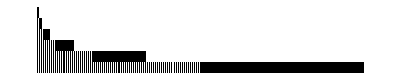

```mathematica
NestList[Flatten[Partition[Flatten[#],3,1]]&,{1,1,0,1,1,1,0},5]//ArrayPlot
```

```mathematica
DownLoad
```

```mathematica
a=0;URLSave[#, FileNameJoin[{"c:\aa", ToString[a++]<>".PDF"}]]&/@w;
```

Syntax::stresc: Unknown string escape \"a".

```mathematica
"http://www.complex-systems.com/pdf/"<>ToString[x]<>".pdf"
```

```mathematica
g=StringCases[#,"Defer["~~a__~~"]"->a]&/@(Tuples[{Range[25], Range[4], Range[4]}] /. {x_,b_, y_} :> ToString[Defer[x-b-y]]);
```

```mathematica
w="http://www.complex-systems.com/pdf/"<>"0"<>#<>".pdf"&/@g;
```

StringJoin::string: String expected at position 2 in "http://www.complex-systems.com/pdf/0" <> 246 <> ".pdf".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

```mathematica
w
```

```mathematica
w={"http://www.complex-systems.com/pdf/10-3-3.pdf","http://www.complex-systems.com/pdf/10-3-4.pdf","http://www.complex-systems.com/pdf/10-4-1.pdf","http://www.complex-systems.com/pdf/10-4-2.pdf","http://www.complex-systems.com/pdf/10-4-3.pdf","http://www.complex-systems.com/pdf/10-4-4.pdf","http://www.complex-systems.com/pdf/11-1-1.pdf","http://www.complex-systems.com/pdf/11-1-2.pdf","http://www.complex-systems.com/pdf/11-1-3.pdf","http://www.complex-systems.com/pdf/11-1-4.pdf","http://www.complex-systems.com/pdf/11-2-1.pdf","http://www.complex-systems.com/pdf/11-2-2.pdf","http://www.complex-systems.com/pdf/11-2-3.pdf","http://www.complex-systems.com/pdf/11-2-4.pdf","http://www.complex-systems.com/pdf/11-3-1.pdf","http://www.complex-systems.com/pdf/11-3-2.pdf","http://www.complex-systems.com/pdf/11-3-3.pdf","http://www.complex-systems.com/pdf/11-3-4.pdf","http://www.complex-systems.com/pdf/11-4-1.pdf","http://www.complex-systems.com/pdf/11-4-2.pdf","http://www.complex-systems.com/pdf/11-4-3.pdf","http://www.complex-systems.com/pdf/11-4-4.pdf","http://www.complex-systems.com/pdf/12-1-1.pdf","http://www.complex-systems.com/pdf/12-1-2.pdf","http://www.complex-systems.com/pdf/12-1-3.pdf","http://www.complex-systems.com/pdf/12-1-4.pdf","http://www.complex-systems.com/pdf/12-2-1.pdf","http://www.complex-systems.com/pdf/12-2-2.pdf","http://www.complex-systems.com/pdf/12-2-3.pdf","http://www.complex-systems.com/pdf/12-2-4.pdf","http://www.complex-systems.com/pdf/12-3-1.pdf","http://www.complex-systems.com/pdf/12-3-2.pdf","http://www.complex-systems.com/pdf/12-3-3.pdf","http://www.complex-systems.com/pdf/12-3-4.pdf","http://www.complex-systems.com/pdf/12-4-1.pdf","http://www.complex-systems.com/pdf/12-4-2.pdf","http://www.complex-systems.com/pdf/12-4-3.pdf","http://www.complex-systems.com/pdf/12-4-4.pdf","http://www.complex-systems.com/pdf/13-1-1.pdf","http://www.complex-systems.com/pdf/13-1-2.pdf","http://www.complex-systems.com/pdf/13-1-3.pdf","http://www.complex-systems.com/pdf/13-1-4.pdf","http://www.complex-systems.com/pdf/13-2-1.pdf","http://www.complex-systems.com/pdf/13-2-2.pdf","http://www.complex-systems.com/pdf/13-2-3.pdf","http://www.complex-systems.com/pdf/13-2-4.pdf","http://www.complex-systems.com/pdf/13-3-1.pdf","http://www.complex-systems.com/pdf/13-3-2.pdf","http://www.complex-systems.com/pdf/13-3-3.pdf","http://www.complex-systems.com/pdf/13-3-4.pdf","http://www.complex-systems.com/pdf/13-4-1.pdf","http://www.complex-systems.com/pdf/13-4-2.pdf","http://www.complex-systems.com/pdf/13-4-3.pdf","http://www.complex-systems.com/pdf/13-4-4.pdf","http://www.complex-systems.com/pdf/14-1-1.pdf","http://www.complex-systems.com/pdf/14-1-2.pdf","http://www.complex-systems.com/pdf/14-1-3.pdf","http://www.complex-systems.com/pdf/14-1-4.pdf","http://www.complex-systems.com/pdf/14-2-1.pdf","http://www.complex-systems.com/pdf/14-2-2.pdf","http://www.complex-systems.com/pdf/14-2-3.pdf","http://www.complex-systems.com/pdf/14-2-4.pdf","http://www.complex-systems.com/pdf/14-3-1.pdf","http://www.complex-systems.com/pdf/14-3-2.pdf","http://www.complex-systems.com/pdf/14-3-3.pdf","http://www.complex-systems.com/pdf/14-3-4.pdf","http://www.complex-systems.com/pdf/14-4-1.pdf","http://www.complex-systems.com/pdf/14-4-2.pdf","http://www.complex-systems.com/pdf/14-4-3.pdf","http://www.complex-systems.com/pdf/14-4-4.pdf","http://www.complex-systems.com/pdf/15-1-1.pdf","http://www.complex-systems.com/pdf/15-1-2.pdf","http://www.complex-systems.com/pdf/15-1-3.pdf","http://www.complex-systems.com/pdf/15-1-4.pdf","http://www.complex-systems.com/pdf/15-2-1.pdf","http://www.complex-systems.com/pdf/15-2-2.pdf","http://www.complex-systems.com/pdf/15-2-3.pdf","http://www.complex-systems.com/pdf/15-2-4.pdf","http://www.complex-systems.com/pdf/15-3-1.pdf","http://www.complex-systems.com/pdf/15-3-2.pdf","http://www.complex-systems.com/pdf/15-3-3.pdf","http://www.complex-systems.com/pdf/15-3-4.pdf","http://www.complex-systems.com/pdf/15-4-1.pdf","http://www.complex-systems.com/pdf/15-4-2.pdf","http://www.complex-systems.com/pdf/15-4-3.pdf","http://www.complex-systems.com/pdf/15-4-4.pdf","http://www.complex-systems.com/pdf/16-1-1.pdf","http://www.complex-systems.com/pdf/16-1-2.pdf","http://www.complex-systems.com/pdf/16-1-3.pdf","http://www.complex-systems.com/pdf/16-1-4.pdf","http://www.complex-systems.com/pdf/16-2-1.pdf","http://www.complex-systems.com/pdf/16-2-2.pdf","http://www.complex-systems.com/pdf/16-2-3.pdf","http://www.complex-systems.com/pdf/16-2-4.pdf","http://www.complex-systems.com/pdf/16-3-1.pdf","http://www.complex-systems.com/pdf/16-3-2.pdf","http://www.complex-systems.com/pdf/16-3-3.pdf","http://www.complex-systems.com/pdf/16-3-4.pdf","http://www.complex-systems.com/pdf/16-4-1.pdf","http://www.complex-systems.com/pdf/16-4-2.pdf","http://www.complex-systems.com/pdf/16-4-3.pdf","http://www.complex-systems.com/pdf/16-4-4.pdf","http://www.complex-systems.com/pdf/17-1-1.pdf","http://www.complex-systems.com/pdf/17-1-2.pdf","http://www.complex-systems.com/pdf/17-1-3.pdf","http://www.complex-systems.com/pdf/17-1-4.pdf","http://www.complex-systems.com/pdf/17-2-1.pdf","http://www.complex-systems.com/pdf/17-2-2.pdf","http://www.complex-systems.com/pdf/17-2-3.pdf","http://www.complex-systems.com/pdf/17-2-4.pdf","http://www.complex-systems.com/pdf/17-3-1.pdf","http://www.complex-systems.com/pdf/17-3-2.pdf","http://www.complex-systems.com/pdf/17-3-3.pdf","http://www.complex-systems.com/pdf/17-3-4.pdf","http://www.complex-systems.com/pdf/17-4-1.pdf","http://www.complex-systems.com/pdf/17-4-2.pdf","http://www.complex-systems.com/pdf/17-4-3.pdf","http://www.complex-systems.com/pdf/17-4-4.pdf","http://www.complex-systems.com/pdf/18-1-1.pdf","http://www.complex-systems.com/pdf/18-1-2.pdf","http://www.complex-systems.com/pdf/18-1-3.pdf","http://www.complex-systems.com/pdf/18-1-4.pdf","http://www.complex-systems.com/pdf/18-2-1.pdf","http://www.complex-systems.com/pdf/18-2-2.pdf","http://www.complex-systems.com/pdf/18-2-3.pdf","http://www.complex-systems.com/pdf/18-2-4.pdf","http://www.complex-systems.com/pdf/18-3-1.pdf","http://www.complex-systems.com/pdf/18-3-2.pdf","http://www.complex-systems.com/pdf/18-3-3.pdf","http://www.complex-systems.com/pdf/18-3-4.pdf","http://www.complex-systems.com/pdf/18-4-1.pdf","http://www.complex-systems.com/pdf/18-4-2.pdf","http://www.complex-systems.com/pdf/18-4-3.pdf","http://www.complex-systems.com/pdf/18-4-4.pdf","http://www.complex-systems.com/pdf/19-1-1.pdf","http://www.complex-systems.com/pdf/19-1-2.pdf","http://www.complex-systems.com/pdf/19-1-3.pdf","http://www.complex-systems.com/pdf/19-1-4.pdf","http://www.complex-systems.com/pdf/19-2-1.pdf","http://www.complex-systems.com/pdf/19-2-2.pdf","http://www.complex-systems.com/pdf/19-2-3.pdf","http://www.complex-systems.com/pdf/19-2-4.pdf","http://www.complex-systems.com/pdf/19-3-1.pdf","http://www.complex-systems.com/pdf/19-3-2.pdf","http://www.complex-systems.com/pdf/19-3-3.pdf","http://www.complex-systems.com/pdf/19-3-4.pdf","http://www.complex-systems.com/pdf/19-4-1.pdf","http://www.complex-systems.com/pdf/19-4-2.pdf","http://www.complex-systems.com/pdf/19-4-3.pdf","http://www.complex-systems.com/pdf/19-4-4.pdf","http://www.complex-systems.com/pdf/20-1-1.pdf","http://www.complex-systems.com/pdf/20-1-2.pdf","http://www.complex-systems.com/pdf/20-1-3.pdf","http://www.complex-systems.com/pdf/20-1-4.pdf","http://www.complex-systems.com/pdf/20-2-1.pdf","http://www.complex-systems.com/pdf/20-2-2.pdf","http://www.complex-systems.com/pdf/20-2-3.pdf","http://www.complex-systems.com/pdf/20-2-4.pdf","http://www.complex-systems.com/pdf/20-3-1.pdf","http://www.complex-systems.com/pdf/20-3-2.pdf","http://www.complex-systems.com/pdf/20-3-3.pdf","http://www.complex-systems.com/pdf/20-3-4.pdf","http://www.complex-systems.com/pdf/20-4-1.pdf","http://www.complex-systems.com/pdf/20-4-2.pdf","http://www.complex-systems.com/pdf/20-4-3.pdf","http://www.complex-systems.com/pdf/20-4-4.pdf","http://www.complex-systems.com/pdf/21-1-1.pdf","http://www.complex-systems.com/pdf/21-1-2.pdf","http://www.complex-systems.com/pdf/21-1-3.pdf","http://www.complex-systems.com/pdf/21-1-4.pdf","http://www.complex-systems.com/pdf/21-2-1.pdf","http://www.complex-systems.com/pdf/21-2-2.pdf","http://www.complex-systems.com/pdf/21-2-3.pdf","http://www.complex-systems.com/pdf/21-2-4.pdf","http://www.complex-systems.com/pdf/21-3-1.pdf","http://www.complex-systems.com/pdf/21-3-2.pdf","http://www.complex-systems.com/pdf/21-3-3.pdf","http://www.complex-systems.com/pdf/21-3-4.pdf","http://www.complex-systems.com/pdf/21-4-1.pdf","http://www.complex-systems.com/pdf/21-4-2.pdf","http://www.complex-systems.com/pdf/21-4-3.pdf","http://www.complex-systems.com/pdf/21-4-4.pdf","http://www.complex-systems.com/pdf/22-1-1.pdf","http://www.complex-systems.com/pdf/22-1-2.pdf","http://www.complex-systems.com/pdf/22-1-3.pdf","http://www.complex-systems.com/pdf/22-1-4.pdf","http://www.complex-systems.com/pdf/22-2-1.pdf","http://www.complex-systems.com/pdf/22-2-2.pdf","http://www.complex-systems.com/pdf/22-2-3.pdf","http://www.complex-systems.com/pdf/22-2-4.pdf","http://www.complex-systems.com/pdf/22-3-1.pdf","http://www.complex-systems.com/pdf/22-3-2.pdf","http://www.complex-systems.com/pdf/22-3-3.pdf","http://www.complex-systems.com/pdf/22-3-4.pdf","http://www.complex-systems.com/pdf/22-4-1.pdf","http://www.complex-systems.com/pdf/22-4-2.pdf","http://www.complex-systems.com/pdf/22-4-3.pdf","http://www.complex-systems.com/pdf/22-4-4.pdf","http://www.complex-systems.com/pdf/23-1-1.pdf","http://www.complex-systems.com/pdf/23-1-2.pdf","http://www.complex-systems.com/pdf/23-1-3.pdf","http://www.complex-systems.com/pdf/23-1-4.pdf","http://www.complex-systems.com/pdf/23-2-1.pdf","http://www.complex-systems.com/pdf/23-2-2.pdf","http://www.complex-systems.com/pdf/23-2-3.pdf","http://www.complex-systems.com/pdf/23-2-4.pdf","http://www.complex-systems.com/pdf/23-3-1.pdf","http://www.complex-systems.com/pdf/23-3-2.pdf","http://www.complex-systems.com/pdf/23-3-3.pdf","http://www.complex-systems.com/pdf/23-3-4.pdf","http://www.complex-systems.com/pdf/23-4-1.pdf","http://www.complex-systems.com/pdf/23-4-2.pdf","http://www.complex-systems.com/pdf/23-4-3.pdf","http://www.complex-systems.com/pdf/23-4-4.pdf","http://www.complex-systems.com/pdf/24-1-1.pdf","http://www.complex-systems.com/pdf/24-1-2.pdf","http://www.complex-systems.com/pdf/24-1-3.pdf","http://www.complex-systems.com/pdf/24-1-4.pdf","http://www.complex-systems.com/pdf/24-2-1.pdf","http://www.complex-systems.com/pdf/24-2-2.pdf","http://www.complex-systems.com/pdf/24-2-3.pdf","http://www.complex-systems.com/pdf/24-2-4.pdf","http://www.complex-systems.com/pdf/24-3-1.pdf","http://www.complex-systems.com/pdf/24-3-2.pdf","http://www.complex-systems.com/pdf/24-3-3.pdf","http://www.complex-systems.com/pdf/24-3-4.pdf","http://www.complex-systems.com/pdf/24-4-1.pdf","http://www.complex-systems.com/pdf/24-4-2.pdf","http://www.complex-systems.com/pdf/24-4-3.pdf","http://www.complex-systems.com/pdf/24-4-4.pdf","http://www.complex-systems.com/pdf/25-1-1.pdf","http://www.complex-systems.com/pdf/25-1-2.pdf","http://www.complex-systems.com/pdf/25-1-3.pdf","http://www.complex-systems.com/pdf/25-1-4.pdf","http://www.complex-systems.com/pdf/25-2-1.pdf","http://www.complex-systems.com/pdf/25-2-2.pdf","http://www.complex-systems.com/pdf/25-2-3.pdf","http://www.complex-systems.com/pdf/25-2-4.pdf","http://www.complex-systems.com/pdf/25-3-1.pdf","http://www.complex-systems.com/pdf/25-3-2.pdf","http://www.complex-systems.com/pdf/25-3-3.pdf","http://www.complex-systems.com/pdf/25-3-4.pdf","http://www.complex-systems.com/pdf/25-4-1.pdf","http://www.complex-systems.com/pdf/25-4-2.pdf","http://www.complex-systems.com/pdf/25-4-3.pdf","http://www.complex-systems.com/pdf/25-4-4.pdf"}
```

{http://www.complex-systems.com/pdf/10-3-3.pdf,http://www.complex-systems.com/pdf/10-3-4.pdf,http://www.complex-systems.com/pdf/10-4-1.pdf,http://www.complex-systems.com/pdf/10-4-2.pdf,http://www.complex-systems.com/pdf/10-4-3.pdf,http://www.complex-systems.com/pdf/10-4-4.pdf,http://www.complex-systems.com/pdf/11-1-1.pdf,http://www.complex-systems.com/pdf/11-1-2.pdf,http://www.complex-systems.com/pdf/11-1-3.pdf,http://www.complex-systems.com/pdf/11-1-4.pdf,http://www.complex-systems.com/pdf/11-2-1.pdf,http://www.complex-systems.com/pdf/11-2-2.pdf,http://www.complex-systems.com/pdf/11-2-3.pdf,http://www.complex-systems.com/pdf/11-2-4.pdf,http://www.complex-systems.com/pdf/11-3-1.pdf,http://www.complex-systems.com/pdf/11-3-2.pdf,http://www.complex-systems.com/pdf/11-3-3.pdf,http://www.complex-systems.com/pdf/11-3-4.pdf,http://www.complex-systems.com/pdf/11-4-1.pdf,http://www.complex-systems.com/pdf/11-4-2.pdf,http://www.complex-systems.com/pdf/11-4-3.pdf,http://www.complex-systems.com/pdf/11-4-4.pdf,http://www.complex-systems.com/pdf/12-1-1.pdf,http://www.complex-systems.com/pdf/12-1-2.pdf,http://www.complex-systems.com/pdf/12-1-3.pdf,http://www.complex-systems.com/pdf/12-1-4.pdf,http://www.complex-systems.com/pdf/12-2-1.pdf,http://www.complex-systems.com/pdf/12-2-2.pdf,http://www.complex-systems.com/pdf/12-2-3.pdf,http://www.complex-systems.com/pdf/12-2-4.pdf,http://www.complex-systems.com/pdf/12-3-1.pdf,http://www.complex-systems.com/pdf/12-3-2.pdf,http://www.complex-systems.com/pdf/12-3-3.pdf,http://www.complex-systems.com/pdf/12-3-4.pdf,http://www.complex-systems.com/pdf/12-4-1.pdf,http://www.complex-systems.com/pdf/12-4-2.pdf,http://www.complex-systems.com/pdf/12-4-3.pdf,http://www.complex-systems.com/pdf/12-4-4.pdf,http://www.complex-systems.com/pdf/13-1-1.pdf,http://www.complex-systems.com/pdf/13-1-2.pdf,http://www.complex-systems.com/pdf/13-1-3.pdf,http://www.complex-systems.com/pdf/13-1-4.pdf,http://www.complex-systems.com/pdf/13-2-1.pdf,http://www.complex-systems.com/pdf/13-2-2.pdf,http://www.complex-systems.com/pdf/13-2-3.pdf,http://www.complex-systems.com/pdf/13-2-4.pdf,http://www.complex-systems.com/pdf/13-3-1.pdf,http://www.complex-systems.com/pdf/13-3-2.pdf,http://www.complex-systems.com/pdf/13-3-3.pdf,http://www.complex-systems.com/pdf/13-3-4.pdf,http://www.complex-systems.com/pdf/13-4-1.pdf,http://www.complex-systems.com/pdf/13-4-2.pdf,http://www.complex-systems.com/pdf/13-4-3.pdf,http://www.complex-systems.com/pdf/13-4-4.pdf,http://www.complex-systems.com/pdf/14-1-1.pdf,http://www.complex-systems.com/pdf/14-1-2.pdf,http://www.complex-systems.com/pdf/14-1-3.pdf,http://www.complex-systems.com/pdf/14-1-4.pdf,http://www.complex-systems.com/pdf/14-2-1.pdf,http://www.complex-systems.com/pdf/14-2-2.pdf,http://www.complex-systems.com/pdf/14-2-3.pdf,http://www.complex-systems.com/pdf/14-2-4.pdf,http://www.complex-systems.com/pdf/14-3-1.pdf,http://www.complex-systems.com/pdf/14-3-2.pdf,http://www.complex-systems.com/pdf/14-3-3.pdf,http://www.complex-systems.com/pdf/14-3-4.pdf,http://www.complex-systems.com/pdf/14-4-1.pdf,http://www.complex-systems.com/pdf/14-4-2.pdf,http://www.complex-systems.com/pdf/14-4-3.pdf,http://www.complex-systems.com/pdf/14-4-4.pdf,http://www.complex-systems.com/pdf/15-1-1.pdf,http://www.complex-systems.com/pdf/15-1-2.pdf,http://www.complex-systems.com/pdf/15-1-3.pdf,http://www.complex-systems.com/pdf/15-1-4.pdf,http://www.complex-systems.com/pdf/15-2-1.pdf,http://www.complex-systems.com/pdf/15-2-2.pdf,http://www.complex-systems.com/pdf/15-2-3.pdf,http://www.complex-systems.com/pdf/15-2-4.pdf,http://www.complex-systems.com/pdf/15-3-1.pdf,http://www.complex-systems.com/pdf/15-3-2.pdf,http://www.complex-systems.com/pdf/15-3-3.pdf,http://www.complex-systems.com/pdf/15-3-4.pdf,http://www.complex-systems.com/pdf/15-4-1.pdf,http://www.complex-systems.com/pdf/15-4-2.pdf,http://www.complex-systems.com/pdf/15-4-3.pdf,http://www.complex-systems.com/pdf/15-4-4.pdf,http://www.complex-systems.com/pdf/16-1-1.pdf,http://www.complex-systems.com/pdf/16-1-2.pdf,http://www.complex-systems.com/pdf/16-1-3.pdf,http://www.complex-systems.com/pdf/16-1-4.pdf,http://www.complex-systems.com/pdf/16-2-1.pdf,http://www.complex-systems.com/pdf/16-2-2.pdf,http://www.complex-systems.com/pdf/16-2-3.pdf,http://www.complex-systems.com/pdf/16-2-4.pdf,http://www.complex-systems.com/pdf/16-3-1.pdf,http://www.complex-systems.com/pdf/16-3-2.pdf,http://www.complex-systems.com/pdf/16-3-3.pdf,http://www.complex-systems.com/pdf/16-3-4.pdf,http://www.complex-systems.com/pdf/16-4-1.pdf,http://www.complex-systems.com/pdf/16-4-2.pdf,http://www.complex-systems.com/pdf/16-4-3.pdf,http://www.complex-systems.com/pdf/16-4-4.pdf,http://www.complex-systems.com/pdf/17-1-1.pdf,http://www.complex-systems.com/pdf/17-1-2.pdf,http://www.complex-systems.com/pdf/17-1-3.pdf,http://www.complex-systems.com/pdf/17-1-4.pdf,http://www.complex-systems.com/pdf/17-2-1.pdf,http://www.complex-systems.com/pdf/17-2-2.pdf,http://www.complex-systems.com/pdf/17-2-3.pdf,http://www.complex-systems.com/pdf/17-2-4.pdf,http://www.complex-systems.com/pdf/17-3-1.pdf,http://www.complex-systems.com/pdf/17-3-2.pdf,http://www.complex-systems.com/pdf/17-3-3.pdf,http://www.complex-systems.com/pdf/17-3-4.pdf,http://www.complex-systems.com/pdf/17-4-1.pdf,http://www.complex-systems.com/pdf/17-4-2.pdf,http://www.complex-systems.com/pdf/17-4-3.pdf,http://www.complex-systems.com/pdf/17-4-4.pdf,http://www.complex-systems.com/pdf/18-1-1.pdf,http://www.complex-systems.com/pdf/18-1-2.pdf,http://www.complex-systems.com/pdf/18-1-3.pdf,http://www.complex-systems.com/pdf/18-1-4.pdf,http://www.complex-systems.com/pdf/18-2-1.pdf,http://www.complex-systems.com/pdf/18-2-2.pdf,http://www.complex-systems.com/pdf/18-2-3.pdf,http://www.complex-systems.com/pdf/18-2-4.pdf,http://www.complex-systems.com/pdf/18-3-1.pdf,http://www.complex-systems.com/pdf/18-3-2.pdf,http://www.complex-systems.com/pdf/18-3-3.pdf,http://www.complex-systems.com/pdf/18-3-4.pdf,http://www.complex-systems.com/pdf/18-4-1.pdf,http://www.complex-systems.com/pdf/18-4-2.pdf,http://www.complex-systems.com/pdf/18-4-3.pdf,http://www.complex-systems.com/pdf/18-4-4.pdf,http://www.complex-systems.com/pdf/19-1-1.pdf,http://www.complex-systems.com/pdf/19-1-2.pdf,http://www.complex-systems.com/pdf/19-1-3.pdf,http://www.complex-systems.com/pdf/19-1-4.pdf,http://www.complex-systems.com/pdf/19-2-1.pdf,http://www.complex-systems.com/pdf/19-2-2.pdf,http://www.complex-systems.com/pdf/19-2-3.pdf,http://www.complex-systems.com/pdf/19-2-4.pdf,http://www.complex-systems.com/pdf/19-3-1.pdf,http://www.complex-systems.com/pdf/19-3-2.pdf,http://www.complex-systems.com/pdf/19-3-3.pdf,http://www.complex-systems.com/pdf/19-3-4.pdf,http://www.complex-systems.com/pdf/19-4-1.pdf,http://www.complex-systems.com/pdf/19-4-2.pdf,http://www.complex-systems.com/pdf/19-4-3.pdf,http://www.complex-systems.com/pdf/19-4-4.pdf,http://www.complex-systems.com/pdf/20-1-1.pdf,http://www.complex-systems.com/pdf/20-1-2.pdf,http://www.complex-systems.com/pdf/20-1-3.pdf,http://www.complex-systems.com/pdf/20-1-4.pdf,http://www.complex-systems.com/pdf/20-2-1.pdf,http://www.complex-systems.com/pdf/20-2-2.pdf,http://www.complex-systems.com/pdf/20-2-3.pdf,http://www.complex-systems.com/pdf/20-2-4.pdf,http://www.complex-systems.com/pdf/20-3-1.pdf,http://www.complex-systems.com/pdf/20-3-2.pdf,http://www.complex-systems.com/pdf/20-3-3.pdf,http://www.complex-systems.com/pdf/20-3-4.pdf,http://www.complex-systems.com/pdf/20-4-1.pdf,http://www.complex-systems.com/pdf/20-4-2.pdf,http://www.complex-systems.com/pdf/20-4-3.pdf,http://www.complex-systems.com/pdf/20-4-4.pdf,http://www.complex-systems.com/pdf/21-1-1.pdf,http://www.complex-systems.com/pdf/21-1-2.pdf,http://www.complex-systems.com/pdf/21-1-3.pdf,http://www.complex-systems.com/pdf/21-1-4.pdf,http://www.complex-systems.com/pdf/21-2-1.pdf,http://www.complex-systems.com/pdf/21-2-2.pdf,http://www.complex-systems.com/pdf/21-2-3.pdf,http://www.complex-systems.com/pdf/21-2-4.pdf,http://www.complex-systems.com/pdf/21-3-1.pdf,http://www.complex-systems.com/pdf/21-3-2.pdf,http://www.complex-systems.com/pdf/21-3-3.pdf,http://www.complex-systems.com/pdf/21-3-4.pdf,http://www.complex-systems.com/pdf/21-4-1.pdf,http://www.complex-systems.com/pdf/21-4-2.pdf,http://www.complex-systems.com/pdf/21-4-3.pdf,http://www.complex-systems.com/pdf/21-4-4.pdf,http://www.complex-systems.com/pdf/22-1-1.pdf,http://www.complex-systems.com/pdf/22-1-2.pdf,http://www.complex-systems.com/pdf/22-1-3.pdf,http://www.complex-systems.com/pdf/22-1-4.pdf,http://www.complex-systems.com/pdf/22-2-1.pdf,http://www.complex-systems.com/pdf/22-2-2.pdf,http://www.complex-systems.com/pdf/22-2-3.pdf,http://www.complex-systems.com/pdf/22-2-4.pdf,http://www.complex-systems.com/pdf/22-3-1.pdf,http://www.complex-systems.com/pdf/22-3-2.pdf,http://www.complex-systems.com/pdf/22-3-3.pdf,http://www.complex-systems.com/pdf/22-3-4.pdf,http://www.complex-systems.com/pdf/22-4-1.pdf,http://www.complex-systems.com/pdf/22-4-2.pdf,http://www.complex-systems.com/pdf/22-4-3.pdf,http://www.complex-systems.com/pdf/22-4-4.pdf,http://www.complex-systems.com/pdf/23-1-1.pdf,http://www.complex-systems.com/pdf/23-1-2.pdf,http://www.complex-systems.com/pdf/23-1-3.pdf,http://www.complex-systems.com/pdf/23-1-4.pdf,http://www.complex-systems.com/pdf/23-2-1.pdf,http://www.complex-systems.com/pdf/23-2-2.pdf,http://www.complex-systems.com/pdf/23-2-3.pdf,http://www.complex-systems.com/pdf/23-2-4.pdf,http://www.complex-systems.com/pdf/23-3-1.pdf,http://www.complex-systems.com/pdf/23-3-2.pdf,http://www.complex-systems.com/pdf/23-3-3.pdf,http://www.complex-systems.com/pdf/23-3-4.pdf,http://www.complex-systems.com/pdf/23-4-1.pdf,http://www.complex-systems.com/pdf/23-4-2.pdf,http://www.complex-systems.com/pdf/23-4-3.pdf,http://www.complex-systems.com/pdf/23-4-4.pdf,http://www.complex-systems.com/pdf/24-1-1.pdf,http://www.complex-systems.com/pdf/24-1-2.pdf,http://www.complex-systems.com/pdf/24-1-3.pdf,http://www.complex-systems.com/pdf/24-1-4.pdf,http://www.complex-systems.com/pdf/24-2-1.pdf,http://www.complex-systems.com/pdf/24-2-2.pdf,http://www.complex-systems.com/pdf/24-2-3.pdf,http://www.complex-systems.com/pdf/24-2-4.pdf,http://www.complex-systems.com/pdf/24-3-1.pdf,http://www.complex-systems.com/pdf/24-3-2.pdf,http://www.complex-systems.com/pdf/24-3-3.pdf,http://www.complex-systems.com/pdf/24-3-4.pdf,http://www.complex-systems.com/pdf/24-4-1.pdf,http://www.complex-systems.com/pdf/24-4-2.pdf,http://www.complex-systems.com/pdf/24-4-3.pdf,http://www.complex-systems.com/pdf/24-4-4.pdf,http://www.complex-systems.com/pdf/25-1-1.pdf,http://www.complex-systems.com/pdf/25-1-2.pdf,http://www.complex-systems.com/pdf/25-1-3.pdf,http://www.complex-systems.com/pdf/25-1-4.pdf,http://www.complex-systems.com/pdf/25-2-1.pdf,http://www.complex-systems.com/pdf/25-2-2.pdf,http://www.complex-systems.com/pdf/25-2-3.pdf,http://www.complex-systems.com/pdf/25-2-4.pdf,http://www.complex-systems.com/pdf/25-3-1.pdf,http://www.complex-systems.com/pdf/25-3-2.pdf,http://www.complex-systems.com/pdf/25-3-3.pdf,http://www.complex-systems.com/pdf/25-3-4.pdf,http://www.complex-systems.com/pdf/25-4-1.pdf,http://www.complex-systems.com/pdf/25-4-2.pdf,http://www.complex-systems.com/pdf/25-4-3.pdf,http://www.complex-systems.com/pdf/25-4-4.pdf}

```mathematica
SemanticImport["http://www.complex-systems.com","pdf"]
```

SemanticImport::intype: Interpreter type specification "pdf" is invalid.

<!DOCTYPE html PUBLIC "-//W3C//DTD XHTML 1.0 Transitional//EN" "http://www.w3.org/TR/xhtml1/DTD/xhtml1-transitional.dtd">
Invalid
Invalid
Invalid
Invalid
Invalid
Invalid
Invalid
Invalid
Invalid
Invalid
Invalid
Invalid
Invalid
Invalid
Invalid
Invalid
⋮_99
2 levels | 115rowsDataset[{__Association}]

Pdf http://www.complex-systems.com

WolframAlphaQueryResults

```mathematica
StringReverse["Ismail"]
```

liamsI

```mathematica
StringTake[StringJoin[Alphabet[]],5]
```

abcde

```mathematica
Table[StringTake["this is about String",n],{n,#}]&@StringLength["this is about String"]//TableForm
```

t
th
thi
this
this 
this i
this is
this is 
this is a
this is ab
this is abo
this is abou
this is about
this is about 
this is about S
this is about St
this is about Str
this is about Stri
this is about Strin
this is about String

```mathematica
WikipediaData["Coumputer"]
```

Missing[NotAvailable]

```mathematica
StringJoin@FromLetterNumber[RandomInteger[{1,26},1000]]
```

swbusksalexsrzlcfhxpnqmkbnppttkswtrzzycbkvxzapyftwxgaapwhbtvdwlfmnuqrajqxuzgopgbczdjefpnpkayjhevleztcnltodcuclzzxlcdixoepqygswltohpstvhbeckiogejkfodhwaxsbfzuhxiaugfdvkfgbzbdloxgiurwxuzipxthjuwzlqxauvlshochyjkknujwyestjqxbcnrabtaplvapwxpltvzxfzmycdgxlibepyyesvalemdazagrqzaevovazxytaqwsiegpqkbzshklpypqnxodaejqyxsfptwcnvmdhbdycfdrfqvzmhzbxfwzpviersrbvjnfyzfinohiejjumljrlccvywndbkumegldlicmexcaiphvcqtryzhwcrhunghmeozzsadpgefjbchnadsyzrqvcmmhdrblpdgbngkmroijteggxlbbdrnrwdvxxjstsgvdstjevliapbywbtdyugwhniwnzozfgkfyzruhjlvbcfcdtqjartsfvnejcrvxndonvybschgjihljpbkgrvhgofpbfyrrxnedolxarjrrcxmzuualskyrftzvnsxvebcdannwenxjkfahnrmlamcfftofknyyomdhxkpklrrdngrnwtmwgwoznbdfiubdubohabybwuddkiyxqtrmyjjbsgwmhgomilwmouoifmmbmuxxxekeslgtrxrifacxlpvtkieatktaopgkeguwoulduptupjrbpdhffzceyixcqryjjtqcasgvatqvslgbbppyncliqglahbcluhfelyfhythxrqehymxhrlnnsoxmkgjbifjpknxfwijjidydbhlqaexuiilgbylbjibjykdneudzqwsujaexozncoucnscaywicpnifzrzttdegmzjvyyrrpslgmhdqlklgvyugsxfxdfnrinposybgkbaerjxtpczzqzbqssgxohrooqdzqsuasors

```mathematica
WikipediaSearch["الحاسوب","MaxItems"->3]
```

{}

```mathematica
{First[#],Length[#]}&/@(Split[Sort[StringTake[#,1]&/@DictionaryLookup[{"Arabic",All}]]])//Column
```

{*,2}
{),142}
{-,5}
{.,36}
{,,13}
{",15}
{،,460}
{؛,1}
{ء,711}
{أ,124}
{ؤ,15}
{إ,1}
{ئ,130}
{ا,1667}
{ب,1548}
{ة,6358}
{ت,3486}
{ث,239}
{ج,650}
{ح,644}
{خ,174}
{د,1755}
{ذ,118}
{ر,3086}
{ز,568}
{س,1327}
{ش,330}
{ص,245}
{ض,371}
{ط,460}
{ظ,85}
{ع,1145}
{غ,144}
{ـ,4}
{ف,1072}
{ق,1096}
{ك,587}
{ل,2462}
{م,1763}
{ن,4047}
{ه,413}
{و,611}
{ى,458}
{ي,3505}
{ً,127}
{ٌ,8}
{ٍ,17}
{َ,40}
{ُ,8}
{ِ,6}
{ّ,1411}
{ْ,76}
{٠,1}
{ﻻ,1}

```mathematica
DictionaryLookup["English",All]
```

DictionaryLookup[English,All]

```mathematica
DictionaryLookup[{"Arabic"},"ال"~~___]
```

```mathematica
DictionaryLookup[{"ت"~~___}]
```

{تم,تن,تؤس,تاب,تاد,تاذ,تام,تحت,تخأ,ترب,ترك,تضم,تقو,تلأ,تمص,تنأ,تنب,توت,توح,تور,توص,توف,تول,توم,تون,تيب,تيت,تيز,تيم,تين,تﻻآ,تائف,تابث,تابن,تاتف,تادأ,تارب,تارد,تارك,تارم,تازأ,تازه,تاغل,تافص,تافي,تاقد,تالآ,تالب,تالش,تامم,تانأ,تانب,تاوذ,تايط,تايف,تايو,تباب,تباث,تبتك,تبثأ,تبثم,تبثي,تبسإ,تبسح,تبسي,تبلا,تبنإ,تبنم,تبني,تبوه,تتشت,تتشم,تتقإ,تحمس,تحنإ,تحني,تداق,تدلو,تدنم,تراه,تربك,ترذب,تركذ,تروك,تروو,تريب,تريف,تريك,تريو,تسبل,تسوف,تسوي,تسيو,تشفأ,تعضو,تعقو,تغاب,تغوف,تفات,تفاخ,تفخي,تفوس,تقؤم,تقام,تقمإ,تقمب,تقمي,تقول,تكاج,تكسأ,تكسم,تكسي,تلاج,تلاو,تلعج,تلفس,تلمه,تلوس,تلوف,تلوه,تماص,تمشإ,تمشي,تمصب,تمصي,تناك,تنلك,تنيغ,تنيك,تهاب,تهبإ,تهبي,توبأ,توتو,تورج,تورك,توصب,توفخ,توكس,تومن,تومي,تويب,تويز,تياب,تياف,تياك,تياه,تياو,تيرب,تيرك,تيسو,تيقم,تيكب,تيلأ,تيمإ,تيمش,تيمم,تينس,تيوت,تيوج,تيوه,تّبث,تّتف,تّذغ,تّفخ,تّوص,تّيز,تّيم,تﻻدج,تائيه,تاباغ,تابثإ,تابثب,تابجو,تابرض,تابرع,تابن(,تابون,تابّن,تاتقم,تاتقي,تاجرد,تاجوز,تاجوم,تاجيز,تاحاب,تاحاس,تاحتف,تاحفص,تاحمل,تاحول,تادحو,تادعص,تادعم,تاديس,تاذلا,تارتف,تارتل,تارتن,تارجح,تارجه,تاردق,تارشح,تارشن,تارطق,تارفش,تارقف,تارقم,تاركب,تارمق,تازاغ,تاسلج,تاصقر,تاصنم,تاضبن,تاضمو,تاطبر,تاطلج,تاطلس,تاعاس,تاعاق,تاعبق,تاعرس,تاعست,تاغدل,تافذق,تافرش,تافقو,تافلم,تاقاب,تاقبط,تاقرس,تاقري,تاقوأ,تاكبش,تاكرش,تاكعك,تاكيه,تالاح,تالاص,تالبط,تالبق,تالتع,تالجس,تالجع,تالحم,تالدب,تالضع,تالضف,تالفح,تالمح,تاليب,تامتت,تامحش,تامدخ,تامرخ,تامرف,تامصب,تامصو,تامكل,تاملك,تانال,تانكث,تانيج,تاهبج,تاهجو,تاهرأ,تاهمأ,تاودأ,تاوذب,تاوذح,تاورج,تاورف,تاوسك,تاوصأ,تاوصا,تاوضع,تاوطخ,تاولا,تاولص,تاونس,تاونق,تايتف,تايرك,تايلآ,تايمر,تايمك,تايوه,تاّبر,تاّخز,تاّدش,تاّرذ,تاّرم,تاّلس,تاّوق,تبتلا,تبجعأ,تبرلا,تبسلا,تبطاخ,تبكلا,تتشتب,تحبصأ,تحنلا,تحّرس,تخألا,تخبلا,تخيلا,تدوسا,تراتس,تربكم,تربكي,تربلأ,تربلج,تربور,ترتنم,ترتني,تزرحأ,تسرام,تسروف,تسروه,تسريه,تسلوه,تسنيو,تسواف,تسورب,تسورف,تسيام,تسيري,تضيبا,تعنلا,تغابم,تغابي,تفإلا,تفارك,تفخلا,تفللا,تفورك,تفوسم,تفوسي,تقملا,تقولا,تقولل,تلصلا,تلفنم,تليوس,تلَمو,تلّغش,تمخات,تمسلا,تمصلا,تمصُأ,تنارج,تنافأ,تنالب,تنبلا,تنرول,تنسلا,تنملا,تنملب,تنيجن,تنّبأ,تهبلا,تواتس,توافت,توبرم,توبسم,توبكم,توتلا,توجلا,توحلا,توحلل,توحنم,توريب,توصلا,توفخب,توفخم,توقمم,توقوم,توكلأ,تومشم,توملا,توناك,تونيم,توهاك,توهبم,تويلإ,تياود,تيباك,تيبثت,تيبلا,تيبنت,تيجرب,تيجيس,تيذسإ,تيراب,تيراغ,تيراه,تيرتس,تيرتن,تيريم,تيزور,تيساب,تيصلا,تيفيب,تيفيل,تيقوت,تيكاه,تيلوب,تيلوج,تيلوك,تيليج,تيماه,تيمسو,تيملا,تيناج,تينان,تينرب,تينيب,تينيج,تيوصت,تيويه,تُقمي,تّبثت,تّبثم,تّبثي,تّتشم,تّتفم,تّتفي,تّفخم,تّفخي,تّقؤم,تّكنم,تّلمم,تّوصم,تّوصي,تّيبم,تّيزم,تّيزي,تْقَم,تأّشجت,تاءارب,تاءاسإ,تاءاطع,تاءوتن,تائفلا,تائملا,تائيزج,تاباسح,تاباصع,تاباوب,تابثلا,تابحاص,تابساح,تابسرت,تابسلا,تابكرم,تابلقت,تابنلا,تابهلا,تاتابن,تاتفال,تاتفلا,تاجالع,تاجرعت,تاحابس,تاحاسم,تاحتاف,تاحتفب,تاحساك,تاحسمم,تاحطان,تاحنجب,تاحنلا,تاحيفص,تاخسان,تادئار,تادئاص,تاداعإ,تادايز,تادحُو,تاددرت,تادلجم,تادلوم,تاديبم,تاديحو,تاذلاب,تارئاط,تارابع,تاراجت,تارازو,تاراسك,تاراسم,تاراشإ,تاراطق,تاراظن,تاراعش,تاراود,تارايس,تارايط,تاربدم,تاربيل,تارذلا,تارسلا,تارفاص,تارفلا,تاركاذ,تاركذم,تاركلا,تارمحم,تارهلا,تاريثم,تاريحب,تاريصق,تازارط,تازاوج,تازهلا,تازولب,تاسآلا,تاسائر,تاسارد,تاساقم,تاسايق,تاسدعب,تاسيئر,تاشتيل,تاصقار,تاضراع,تاطاسو,تاطبلا,تاططخم,تاطيحم,تاطيلس,تاعئاب,تاعاخن,تاعامج,تاعذال,تاعراق,تاعربت,تاعنام,تاعيبم,تاغارف,تاغللا,تاغيوب,تافآلا,تافذاق,تافصلا,تافيصو,تاقابس,تاقاطب,تاقاقر,تاقالح,تاقالع,تاقبطب,تاقحلم,تاقدلا,تاكسلا,تاكنلا,تاكيلس,تالآلا,تالباق,تالدعم,تالزلا,تالصلا,تالصوم,تاللظم,تالمأت,تالماع,تالواط,تالومح,تاليزم,تامارق,تاماقم,تامالع,تامامح,تامتاك,تامداخ,تامدقم,تامدكل,تامسار,تامسجم,تامسلا,تامظنم,تاملكب,تامملا,تامورك,تاموكح,تاميدع,تانئاك,تانازخ,تانايب,تانبلا,تانحاش,تانميم,تانواب,تانوكم,تانيلا,تانّيع,تاهآلا,تاهجاو,تاوادأ,تاوجيج,تاودأل,تاورضخ,تاوقلا,تاوكول,تاوليك,تايئزج,تايالو,تاياهن,تاياور,تايبرم,تايراس,تايرطف,تايرظن,تايرقف,تايركذ,تايروح,تايرود,تايعار,تايفتك,تايقاط,تايقاو,تايلمع,تايناث,تايوئم,تاّبسم,تاّدعم,تاّذلا,تاّرقم,تاّسجم,تاّصنم,تاّضخم,تاّطحم,تاّكدم,تاّلجس,تاّلجم,تاّلحم,تاّيلآ,تباثلا,تبثملا,تبحسنا,تبنتسإ,تبيركس,تبّسلا,تبّشلا,تتشتلل,تجّوزت,تحّنلا,تخيلاب,تخُألا,ترابوه,تراجوب,تراخلإ,ترازوم,تراكلا,تراكيد,تربتعإ,تربرهل,تربويه,تروبلا,تروبيب,تريبور,تريبوش,تززتها,تسابلا,تسافلب,تستباب,تسرثاب,تسرموس,تسنريإ,تسوكنإ,تسيليس,تشدارز,تفاخلا,تفوسلا,تفيكلا,تفّللا,تقؤملا,تقاملا,تقصتلا,تقولاب,تقوملا,تكرتوي,تكيلير,تلوبيي,تلوفلا,تلِمُع,تماصلا,تمزتلا,تمّصلا,تناكنإ,تنانوك,تنايرب,تنتبلا,تنرتنا,تنميلك,تنوبود,تنومود,تنوميد,تنيسنف,تنيسول,تنيمدأ,توافتب,توافتم,توافتي,توخيلا,تورتشع,توركلا,توصلاب,توعنلا,توفخلا,توفلوف,توفيلت,توكرام,توكسلا,تولراش,تولفلا,تومغرب,توملاب,تومليه,تويبلا,تويرام,تويزلا,تويشاك,توينلا,توّتلا,توّصلا,تيابلا,تيافال,تيالاه,تيانكم,تيانيب,تيبثتب,تيبثتل,تيبروك,تيتكال,تيجيلأ,تيربلف,تيريفإ,تيسلاك,تيسليف,تيضتقا,تيكتوب,تيكسلا,تيكورك,تيلاثف,تيلويه,تيمتسم,تيمروف,تيمريك,تيمليو,تيمملا,تيمورج,تينايس,تينراب,تينراغ,تينريب,تيوكلا,تيّزلا,تيّصلا,تّبثتي,تّتفتم,تّمزتب,تّمزتم,تّنصتم,تّنصتي,تّيملا,تاءارجإ,تاءارجا,تاءاصحإ,تائيبلا,تائيهلا,تاباسحب,تاباغلا,تابتعلا,تابثإلا,تابثإلل,تابثالل,تابثولا,تابجولا,تابدحلا,تابدنلا,تابرضلا,تابرعلا,تابرملا,تابشخلا,تابصقلا,تابطخلا,تابغرلا,تابغزلا,تابقعلا,تابلحلا,تابلطلا,تابلكلا,تابنجلا,تابنكلا,تابورشم,تابونلا,تابيثلا,تابّترم,تابّثلا,تابّعكم,تابّكرم,تابّنلا,تاتابثإ,تاتبرلا,تاتبنلا,تاتسآلا,تاتشألا,تاتنسلا,تاتيربك,تاتّشلا,تاثعبلا,تاجاحلا,تاجردلا,تاجرعلا,تاجعطلا,تاجلاعم,تاجميرب,تاجهللا,تاجوزلا,تاجوملا,تاجيزلا,تاحابلا,تاحاحلإ,تاحالصإ,تاحاولا,تاحتفلا,تاحسملا,تاحفصلا,تاحقولا,تاحمللا,تاحوللا,تاحيصلا,تاحيولت,تاخاّخب,تاخرصلا,تاخضملا,تاخطللا,تاخفنلا,تاداعلا,تاداّدع,تادبزلا,تادحولا,تادرنلا,تادعملا,تادلبلا,تادلجلا,تادلجمب,تادنتسم,تادنسلا,تاديسلا,تادّسجت,تاذيملت,تارأفلا,تارابلا,تاراثيق,تاراحلا,تاراذنإ,تاراغلا,تاراقلا,تاراقلل,تاراكذت,تارالود,تاراّظن,تاراّقن,تاراّود,تاراّيس,تاربقلا,تاربولا,تارتفلا,تارتنلا,تارثبلا,تارجحلا,تارجملا,تارجهلا,تاردقلا,تارذقلا,تارسجلا,تارشحلا,تارشعلا,تارشنلا,تارصتخم,تارصعلا,تارصملا,تارطقلا,تارظنلا,تارعذلا,تارعسلا,تارعشلا,تارفسلا,تارفشلا,تارقفلا,تارقملا,تارقنلا,تاركبلا,تارمتؤم,تارمجلا,تارمسلا,تارمملا,تارمنلا,تارهملا,تاروانم,تاروبلا,تاروثلا,تارودلا,تاروّنت,تاريبيس,تارّافص,تارّبكم,تارّذلا,تازاغلا,تازاّفق,تازخولا,تازرغلا,تازفقلا,تازمغلا,تازيملا,تاساملا,تاسايقب,تاساّرك,تاساّره,تاساّود,تاسجملا,تاسدعلا,تاسسؤمل,تاسكنلا,تاسلجلا,تاسمخلا,تاسمللا,تاسمهلا,تاسنآلا,تاسنبلا,تاسوبلم,تاشاشلا,تاشحجلا,تاشعرلا,تاشيرلا,تاصرقلا,تاصلصلا,تاصنإلا,تاصوبلا,تاصّلقت,تاضافضف,تاضبقلا,تاضبنلا,تاضمولا,تاضوافم,تاضيرحت,تاضيفخت,تاطبارت,تاطحملا,تاطرشلا,تاطرولا,تاطسوتم,تاطقللا,تاطلجلا,تاطلخلا,تاطلسلا,تاطلغلا,تاطّسوت,تاطّشنم,تاطّفنم,تاظاّفح,تاظحللا,تاعاسلا,تاعاعشإ,تاعاقلا,تاعاّقف,تاعاّمش,تاعبسلا,تاعبطلا,تاعبقلا,تاعجارم,تاعجبلا,تاعراصم,تاعرجلا,تاعزنلا,تاعستلا,تاعفترم,تاعفدلا,تاعفصلا,تاعقرلا,تاعلطلا,تاعوطقم,تاعومجم,تاعيبلا,تاعّبق(,تاغبصلا,تاغيلبت,تافاحلا,تافجرلا,تافردلا,تافرشلا,تافرطلا,تافصاوم,تافصولا,تافضرلا,تافقولا,تافلقلا,تافلملا,تافنسلا,تافوفصم,تافّصلا,تافّلخم,تاقابلا,تاقاطلا,تاقاغلا,تاقافخإ,تاقايلا,تاقبطلا,تاقداصم,تاقدصلا,تاقدملا,تاقرسلا,تاقرطلا,تاقرفتم,تاقريلا,تاقصللا,تاقعللا,تاقفدلا,تاقفصلا,تاقفنلا,تاقفنلل,تاقلحلا,تاقلطلا,تاقوألا,تاقوجلا,تاقودلا,تاقولخم,تاقووار,تاقيلعت,تاكبحلا,تاكبشلا,تاكحضلا,تاكربلا,تاكرحلا,تاكرشلا,تاكسإلا,تاكسملا,تاكعكلا,تاكعولا,تاكفملا,تاكلتمم,تاكلملا,تاكّرحت,تالآلاب,تالاحلا,تالاشلا,تالاصتإ,تالاهلا,تالاّسغ,تالاّقث,تالاّمح,تالباقم,تالبنلا,تالتشلا,تالتعلا,تالجسلا,تالجعلا,تالجملا,تالحرلا,تالحملا,تالداعم,تالدبلا,تالدنمس,تالسغلا,تالسملا,تالصخلا,تالصولا,تالضعلا,تالضفلا,تالطبلا,تالظملا,تالعشلا,تالعولا,تالفجلا,تالفحلا,تالكألا,تالكرلا,تالمحلا,تالمعلا,تالوجلا,تالوغلا,تاليجست,تاليدعت,تاليفلا,تاليقلا,تاليلحت,تاليوحت,تالّبقم,تالّتكت,تالّدعم,تالّمجم,تالّهؤم,تالّوحم,تامءاوم,تاماخلا,تاماقلا,تاماهتإ,تاماّمح,تاماّمص,تامجألا,تامجتسإ,تامجهلا,تامحرلا,تامدخلا,تامدصلا,تامدكلا,تامركلا,تامزألا,تامسنلا,تامغنلا,تامكالم,تامكللا,تاملاكم,تاملحلا,تاملظلا,تاملكلا,تامهملا,تامواقم,تامولعم,تاميتلل,تاميخلا,تاميلعت,تامييقت,تامّردم,تامّسلا,تانئاك(,تاناحلا,تاناخلا,تاناطرس,تاناويح,تانحشلا,تانخثُم,تاندهلا,تانردلا,تانسحلا,تانشألا,تانضحلا,تانعطلا,تانعللا,تانفحلا,تانلشلا,تانمسلا,تانميلإ,تانهارم,تانوبرك,تانوزلح,تانومره,تانيابت,تانيجلا,تانيسحت,تانيعلا,تانيفلا,تانيكام,تانّوكم,تانّيعم,تاهاعلا,تاهباشت,تاهبجلا,تاهدرلا,تاهزنلا,تاهكنلا,تاهمألا,تاهوفلا,تاهيجوت,تاهّوشت,تاوبعلا,تاوبللا,تاوجفلا,تاوخألا,تاودألا,تاورثلا,تاورعلا,تاوزغلا,تاوزنلا,تاوسنلق,تاوشحلا,تاوصألا,تاوطخلا,تاوعدلا,تاوفغلا,تاوفهلا,تاولخلا,تاولصلا,تاومألا,تاونقلا,تاوهشلا,تايارلا,تاياشلا,تاياّلغ,تايبنلا,تايتفلا,تايثالث,تايجمرب,تايحتلا,تايحرسم,تايدفلا,تايدملا,تايرابم,تايرثلا,تايرحلا,تايرذلا,تايشحلا,تايشملا,تايصخلا,تايضاير,تايعابر,تايفولا,تايلآلا,تايلباق,تايلصلا,تايلكلا,تايمحلا,تايمرلا,تايمكلا,تاينثلا,تاينجلا,تاينكلا,تايوطلا,تايونلا,تايّالغ,تاّبهلا,تاّتسلا,تاّجحلا,تاّجضلا,تاّحنلا,تاّدجلا,تاّدهلا,تاّرذلا,تاّرملا,تاّرممب,تاّزهلا,تاّشرلا,تاّصتمم,تاّصملا,تاّضعلا,تاّطبلا,تاّفدلا,تاّفكلا,تاّفللا,تاّقدلا,تاّقطلا,تاّكنلا,تاّلزلا,تاّماسم,تاّمعلا,تاّنرلا,تاّوقلا,تاّوكلا,تاّيتوص,تاّيطلا,تاّيعمس,تاّيفنح,تاّيلقع,تاّيلمع,تاّيهفش,تاّيّمك,تباوثلا,تبركسلت,تراهكول,تراوكلا,تراويتس,تروبريف,تروبوين,تروبيرف,تروفنوم,تروكراه,تريبريه,تريبليه,تساكسيم,تسبادوب,تسراخوب,تسريفيا,تسريهمأ,تسيوهلا,تسِثيمأ,تقاوتلا,تكوسنوو,تكيدينب,تكيركلا,تلزابلا,تلفسألا,تليفزور,تماّصلا,تمدختسا,تمزتملا,تنايبما,تنريكوم,تنزويلا,تنمسإلا,تنواميب,تنومديب,تنومريف,تنومكوأ,تنيابلا,تنيبكام,تنيجراس,تنيوجدأ,توارتلا,توافتلا,توباتلا,توبلسلا,تورديرب,توغاطلا,توقايلا,توقمملا,توكتكلا,توكسيرب,توكّسلا,توليماك,تومردكم,تومزبلا,توملغلا,تونيجاه,توهاللا,تياجلوك,تياربيي,تياسكيإ,تيبابلا,تيباجيج,تيبثتلا,تيبثتلل,تيتسجنت,تيتفتلا,تيتكتلا,تيتنيرب,تيثرونأ,تيجديرب,تيجيسكإ,تيربكلا,تيرجرام,تيرفعلا,تيريبلا,تيريفلا,تيساكلا,تيسنووك,تيفختلا,تيفوزلا,تيقوتلا,تيكسملا,تيكنتلا,تيلبيرت,تيلتراب,تيلربلا,تيلورلا,تيليركأ,تيماتلج,تيماليو,تينابرأ,تينونيم,تينيبلا,تينيليس,تيورتيد,تيوصتلا,تييزتلا,تيّرفلا,تِّبثُم,تّبثملا,تّتشتلا,تّفخملا,تّقؤملا,تّقوملا,تّنصتلا,تّيزملا,تْقَملا,تﻻاقملا,تآفاكملا,تاءادألا,تاءادعلا,تاءادنلا,تاءارقلا,تاءاسإلا,تاءاصحإل,تاءافكلا,تاءاقللا,تاءالطلا,تاءالولا,تاءانثلا,تاءانثنإ,تاءانفلا,تاءاوتلا,تاءوبنلا,تاءوتنلا,تاؤبنتلا,تائجهتلا,تائدابلا,تائيزجلا,تائيقملا,تابابدلا,تاباتكلا,تاباجإلا,تاباجحلا,تاباحسلا,تاباذعلا,تابارطضإ,تابارغلا,تابارقلا,تاباسحلا,تاباصإلا,تاباصعلا,تاباطخلا,تاباعدلا,تاباقنلا,تابالحلا,تابالقلا,تابالكلا,تاباوبلا,تاببسملا,تابترملا,تابتكملا,تابجاولا,تابذبذلا,تابرشملا,تابرعلاب,تابرعملا,تابروشلا,تابرّضلا,تابساحلا,تابصّنلا,تابطبطلا,تابطرملا,تابطِخلا,تابقعملا,تابكرملا,تابلعملا,تابلقتلا,تابلقشلا,تابلّطلا,تابمّللا,تابنركلا,تابهارلا,تابوعصلا,تابوقعلا,تابيبحلا,تابيتكلا,تابيذملا,تابيرقلا,تابيصقلا,تابيطخلا,تابيمألا,تاتابنلا,تاتبثملا,تاتبّنلا,تاتسومرث,تاتفاللا,تاتكّسلا,تاتلوفلا,تاتيوكسب,تاثالثلا,تاثلثملا,تاثيرولا,تاجاجزلا,تاجارخلا,تاجاردلا,تاجازملا,تاجالثلا,تاجالزلا,تاجالعلا,تاجانصلا,تاجايتحإ,تاجايتها,تاجتنملا,تاجرخملا,تاجردتلا,تاجردلاب,تاجنشتلا,تاجهوتلا,تاجوّزلا,تاجيوتلا,تاحاجنلا,تاحادقلا,تاحارجلا,تاحاسملا,تاحاشولا,تاحافتلا,تاحاقللا,تاحاقولا,تاحاّسلا,تاحبسملا,تاحشرملا,تاحفّصلا,تاحوتفلا,تاحورشلا,تاحوّللا,تاحيّصلا,تاخابطلا,تاخافتنا,تاخرّصلا,تاخسانلا,تاخيشملا,تادئافلا,تادابإلا,تاداحّتإ,تادادسلا,تادادعلا,تادارإلا,تادازملا,تاداسولا,تادامضلا,تادامكلا,تاداهشلا,تادايدزا,تادايزلا,تادايعلا,تادايقلا,تاددرتلا,تادراطلا,تادراولا,تادربملا,تادرفملا,تادرمتلا,تادرمزلا,تادروللا,تادصاحلا,تادعاقلا,تادعملاب,تادلجملا,تادنّسلا,تادهنتلا,تاديبملا,تاديفحلا,تادّيجلا,تارئاطلا,تارابتخإ,تارابتخا,تارابعلا,تاراثإلا,تاراجفنا,تاراحملا,تارادإلا,تارادصلا,تارادملا,تارارشلا,تارارقلا,تارازملا,تارازولا,تاراسملا,تاراشإلا,تاراصحلا,تاراضحلا,تاراطإلا,تاراطإلل,تاراطعلا,تاراطقلا,تاراطملا,تاراظنلا,تاراعشلا,تاراغملا,تارافحلا,تارافسلا,تاراقعلا,تاراكتحا,تارامإلا,تارامخلا,تارانإلا,تارانفلا,تارانملا,تاراهبلا,تاراهملا,تاراوحلا,تارايتلا,تارايتلل,تارايخلا,تارايزلا,تارايسلا,تارايعلا,تاراّشلا,تاراّيسب,تاراّيّت,تاربنقلا,تاربوألا,تارتجملا,تارتيسلا,تارثؤملا,تارجفملا,تارحاسلا,تارحبملا,تارخؤملا,تارداصلا,تاردخملا,تارشؤملا,تارشّنلا,تارصاخلا,تارضحتسم,تارطاقلا,تارطسقلا,تارعاشلا,تارفاصلا,تارفّشلا,تارقرقلا,تاركذملا,تاركسملا,تاركفملا,تارمدملا,تارهاعلا,تاروبلاب,تارورضلا,تاروزحلا,تاروصتلا,تاروطتلا,تارولبلا,تارولكلا,تارونتلا,تاروّثلا,تاريجشلا,تاريجعلا,تاريحبلا,تاريدملا,تاريرهلا,تاريعشلا,تاريغتلا,تاريمألا,تارّبقلا,تارّنزلا,تازاجإلا,تازارطلا,تازازهلا,تازافقلا,تازاكعلا,تازانجلا,تازايتما,تازجعملا,تازرافلا,تازوجحلا,تازوربلا,تازولبلا,تاسائرلا,تاساردلا,تاساسألا,تاساعتلا,تاساقملا,تاساودلا,تاسايسلا,تاسدسملا,تاسدقملا,تاسرافلا,تاسسؤملا,تاسفنخلا,تاسكاعلا,تاسكافلا,تاسموملا,تاسناعلا,تاسنوألا,تاسورعلا,تاسوقتلا,تاسيئرلا,تاسيسبلا,تاسيلكنأ,تاشابحلا,تاشارفلا,تاشاشرلا,تاشاعملا,تاشالفلا,تاشخشخلا,تاشماكلا,تاشيودنس,تاصاصقلا,تاصاصملا,تاصالخلا,تاصاوغلا,تاصحافلا,تاصقارلا,تاصقّرلا,تاصوحفلا,تاضايرلا,تاضراعلا,تاضرمملا,تاطاسبلا,تاطاشنلا,تاطاطنلا,تاطالخلا,تاطايخلا,تاطبخللا,تاطشاملا,تاطشكملا,تاططخملا,تاطقاسلا,تاطقسملا,تاطوغضلا,تاطيحملا,تاطيحملل,تاظفاحلا,تاعئابلا,تاعئاشلا,تاعابطلا,تاعاجملا,تاعاذإلا,تاعاربلا,تاعاريلا,تاعازنلا,تاعاشإلا,تاعاشبلا,تاعاطقلا,تاعاظفلا,تاعافدلا,تاعافللا,تاعاقفلا,تاعامتجا,تاعامجلا,تاعامسلا,تاعانصلا,تاعانملا,تاعاّسلا,تاعباطلا,تاعبرألا,تاعبرملا,تاعدوتسم,تاعربتلا,تاعردملا,تاعرسملا,تاعرّسلا,تاعزفملا,تاعطاقلا,تاعفارلا,تاعفّدلا,تاعقرفلا,تاعماجلا,تاعماقلا,تاعمجتلا,تاعمجملا,تاعناملا,تاعورزلا,تاعونملا,تاعيبملا,تاعّبقلا,تاعّردمب,تاغارفلا,تاغايصلا,تاغيوبلا,تافاتهلا,تافاثكلا,تافاخسلا,تافارجلا,تافارحنا,تافارخلا,تافارزلا,تافارطلا,تافارعلا,تافاسملا,تافاضإلا,تافاطخلا,تافاقثلا,تافالخلا,تافاوطلا,تافثكملا,تافدغملا,تافذاقلا,تافرصتلا,تافرعملا,تافرغملا,تافرّطلا,تافسلفلا,تافسوفلا,تافشاكلا,تافصاعلا,تاففجملا,تافقوتلا,تافلآتلا,تافلختلا,تافوذحلا,تافوشكلا,تافيرخلا,تافيصولا,تافّصلاب,تاقابسلا,تاقادصلا,تاقارتخإ,تاقاطبلا,تاقاعإلا,تاقالطلا,تاقالعلا,تاقامحلا,تاقايسلا,تاقايللا,تاقبّطلا,تاقدّصلا,تاقراحلا,تاقربملا,تاقزعملا,تاقسافلا,تاقشمملا,تاقصاللا,تاقصلملا,تاقفخملا,تاقفدتلا,تاقفرملا,تاقفّصلا,تاقفّنلا,تاقلزملا,تاقلطملا,تاقيدصلا,تاقيشعلا,تاكارشلا,تاكالملا,تاكبوبلا,تاكبّشلا,تاكرحتلا,تاكرشلاب,تاكريسلا,تاكرّتلا,تاكنرفلا,تالئاعلا,تالاجملا,تالاحإلا,تالادهلا,تالازإلا,تالاصألا,تالافتحإ,تالافسلا,تالافكلا,تالاقسلا,تالاقملا,تالاكولا,تالالدلا,تالالسلا,تالالشلا,تالامإلا,تالامزلا,تالاوحلا,تالايخلا,تالايرلا,تالباكلا,تالبورلا,تالتكتلا,تالجسملا,تالحنملا,تالخدتلا,تالخدملا,تالداحلا,تالدانلا,تالدعملا,تالدهتلا,تالزعملا,تالسرملا,تالصافلا,تالصحملا,تالصفملا,تالصوبلا,تالصوحلا,تالصوملا,تالضعلاب,تالضعملا,تالظملاب,تالعشملا,تالعّشلا,تالفاحلا,تالقانلا,تالكآتلا,تالكشملا,تاللخملا,تالمأتلا,تالماحلا,تالمكتلا,تالمهملا,تالهؤملا,تالهسملا,تالوبملا,تالوحملا,تالوسنوك,تالوطبلا,تالوفطلا,تالومحلا,تاليختلا,تاليدعلا,تاليرملا,تاليزملا,تامئاقلا,تاماخرلا,تامارغلا,تاماركلا,تاماسرلا,تاماسملا,تاماعدلا,تاماعزلا,تاماعنلا,تاماقإلا,تاماقملا,تامالعلا,تامامتهإ,تامامحلا,تامامصلا,تامامكلا,تاماهشلا,تاماودلا,تامتمتلا,تامجرتلا,تامحّللا,تامداخلا,تامدقملا,تامدوملا,تامدّصلا,تامرذهلا,تامزلتسم,تامسارلا,تامظنملا,تامغّنلا,تامقعملا,تامكّللا,تامنيسلا,تامهمهلا,تاموركلا,تاموسرلا,تاموصخلا,تاموكحلا,تامولعمل,تاميادلا,تاميخملا,تاميلحلا,تانئاخلا,تانئاكلا,تاناحتما,تانادإلا,تانازخلا,تاناضحلا,تاناطبلا,تاناعإلا,تانامألا,تانامضلا,تانامكلا,تاناهإلا,تاناوطسإ,تانايبلا,تانايخلا,تانايكلا,تانتافلا,تانجعملا,تانحاشلا,تاندندلا,تانرقملا,تانضاحلا,تانطلسلا,تانكّللا,تانليثيإ,تاننسملا,تانهاكلا,تانهوملا,تانوابلا,تانواهلا,تانوكملا,تانولطنب,تانوهرلا,تانويآلا,تانويألا,تانويسكأ,تانيطبلا,تانيعملا,تانيمولأ,تانينتلا,تانّيعلا,تاهاتملا,تاهافتلا,تاهجاولا,تاهجوملا,تاهزّنلا,تاهقهقلا,تاهويدار,تاهينجلا,تاهّمألا,تاوادعلا,تاوارهلا,تاوافطلا,تاواقنلا,تاوالصلا,تاوالعلا,تاوامسلا,تاودرخلا,تاوشّنلا,تاونّسلا,تايادبلا,تايافنلا,تاياقسلا,تاياقولا,تاياكحلا,تايالغلا,تايالولا,تايالولل,تايامحلا,تاياهنلا,تاياورلا,تاياوشلا,تاياوهلا,تاياّرلا,تايبرألا,تايبرملا,تايبعشلا,تايبورلا,تايبوللا,تايتقإلا,تايتوصلا,تايثرملا,تايجاحلا,تايجنزلا,تايحضتلا,تايدحتلا,تايدلبلا,تايراسلا,تايرثألا,تايرخسلا,تايردصلا,تايرصبلا,تايرطفلا,تايرظنلا,تايرفحلا,تايركذلا,تايرهزلا,تايروحلا,تايرودلا,تايزاوتم,تايسمألا,تايسمشلا,تايسنجلا,تايصخشلا,تايصوتلا,تايضرألا,تايضرفلا,تايضمحلا,تايطرشلا,تايظحملا,تايعارلا,تايعبتلا,تايعمجلا,تايعمسلا,تايعونلا,تايغابلا,تايفشتسم,تايفصتلا,تايفلألا,تايفلتلا,تايفنحلا,تايقاولا,تايقربلا,تايقرتلا,تايقنتلا,تايقودلا,تايكزتلا,تايكلملا,تايلاجلا,تايلزهلا,تايلصملا,تايلعتلا,تايلكشلا,تايلمعلا,تايليثمت,تايماحلا,تايماسلا,تايمويلا,تايمّرلا,تاينقتلا,تاينمألا,تايهلإلا,تايوئملا,تايواحلا,تايواغلا,تايواهلا,تايوتحمل,تايوحرلا,تايوستلا,تايوضعلا,تايولحلا,تاييدثلا,تايّلكلا,تايّنجلا,تاّبصملا,تاّحصملا,تاّحّنلا,تاّخضملا,تاّدخملا,تاّدصملا,تاّدعملا,تاّدّشلا,تاّذّللا,تاّرجملا,تاّرسملا,تاّرقملا,تاّرمملا,تاّرّذلا,تاّزيملا,تاّشحملا,تاّشرملا,تاّشقملا,تاّصاملا,تاّصقملا,تاّصنملا,تاّطحملا,تاّفاحلا,تاّفلملا,تاّقّدلا,تاّكفملا,تاّلظملا,تاّلّسلا,تاّمهملا,تاّوتفلا,تاّيئاجه,تاّيئادن,تاّيئانث,تاّيئيزج,تاّيجمرب,تاّيحتلا,تاّيحرسم,تاّيداحأ,تاّيركلا,تاّيضاير,تاّيعابر,تاّيفولا,تاّيلباق,تاّيلكلا,تاّيمكلا,تاّيهيدب,تاّيوهلا,تبنتسملا,تبوليكلا,تدراهنير,تدلوبموه,تدلوهنير,ترابانوب,تراهينير,تروبتسيو,ترورديبس,تروورفيل,ترووسوال,تروولكيس,ترووليوك,تروونروه,تسرهينيب,تسروهملإ,تسرووتلب,تسرووكوب,تسيركليج,تسيركليه,تشتيربلأ,تفلدنقلا,تفوركناب,تكيلويدإ,تلابوكلا,تلاطشجلا,تنرتنإلا,تنرتنالا,تنرثيإلا,تنمسألاب,تنوكيفلا,تنومريلك,تواثراوس,توباتسور,توبكنعلا,توبموكلا,توبوّرلا,توروويكس,توريكانس,توشريفوأ,تونكنبلا,توهاّللا,تويراكوي,تياباجيم,تياباغيم,تياجرتاو,تياجوألا,تياربلوأ,تيارتراك,تياريتال,تياسيدنأ,تيانيلاج,تيباوتلا,تيبثّتلا,تيبثّتلل,تيبوليرت,تيتفّتلا,تيدبيلوم,تيرافعلا,تيرالكلا,تيربكلاب,تيرولفلا,تيسكوبلا,تيسوكلاش,تيقوّتلا,تيكاتكلا,تيكوتنان,تيكيركلا,تيلكابلا,تينامألا,تيناوطنأ,تينلوكلا,تيوصّتلا,تيوكسبلا,تييتفتلا,تييفوسلا,تِّبثملا,تّتشّتلا,تّصنتملا,تّمزّتلا,تّنصتملا,تﻻذتبملا,تاءارجإلا,تاءارغإلا,تاءاشنإلا,تاءاصحإلا,تاءاغلإلا,تاءافغإلا,تاءاقّللا,تاءالّطلا,تاءامغإلا,تاءاميإلا,تاءاوغإلا,تاءاوّللا,تائجافملا,تائفاكملا,تائوتّنلا,تائيربتلا,تائّدهملا,تابارطضال,تاباهسإلا,تاباّبسلا,تاباّحسلا,تاباّوبلا,تابذبذتلا,تابذبذملا,تابراحملا,تابراضتلا,تابراقتلا,تابسانملا,تابعادملا,تابقارملا,تابقاعتلا,تابكيوكلا,تابلاطملا,تابلاّطلا,تابلطتملا,تابنتسإلا,تابورشملا,تابوساحلا,تابيترتلا,تابيذكتلا,تابيرختلا,تابيردتلا,تابيصقلاب,تابيكرتلا,تابّدحتلا,تابّرستلا,تابّسرتلا,تابّصخملا,تابّعكملا,تابّقعتلا,تابّكرملا,تابّلقتلا,تابّنذملا,تابّيتكلا,تاتابّنلا,تاتانوسلا,تاتاّحنلا,تاتراوكلا,تاتسوربلا,تاتنيابلا,تاتوافتلا,تاتيربكلا,تاتيساكلا,تاتيوصتلا,تاتّبثملا,تاتّفخملا,تاتّقوملا,تاثداحملا,تاثدحتملا,تاثيدحتلا,تاثّولملا,تاجاجّزلا,تاجالزملا,تاجاّردلا,تاجلاعملا,تاجنفسإلا,تاجودزملا,تاجورحدلا,تاجوسنملا,تاجيردتلا,تاجيومتلا,تاجّردملا,تاجّرعتلا,تاجّنشتلا,تاجّومتلا,تاجّيهتلا,تاجّيهملا,تاحاضيإلا,تاحالصإلا,تاحاّتفلا,تاحاّفللا,تاحتافملا,تاحرتقملا,تاحلطصملا,تاحورطإلا,تاحورطملا,تاحومّطلا,تاحيحصتلا,تاحيرصتلا,تاحيشرتلا,تاحيضوتلا,تاحيفصتلا,تاحيلصتلا,تاحيملتلا,تاحيولتلا,تاحّقنملا,تاحّنرتلا,تاحّيقتلا,تاخابّطلا,تاخاّبطلا,تاخاّخبلا,تاخوفايلا,تاخيرأتلا,تاخينرزلا,تادئاّزلا,تاداحتإلا,تادادعإلا,تادارافلا,تاداريإلا,تاداسفإلا,تاداشرإلا,تادامّضلا,تاداهّشلا,تادايصملا,تاداّبللا,تاداّدسلا,تاداّدعلا,تاداّرطلا,تاداّمكلا,تادراطملا,تادعاسملا,تادعاّصلا,تادقتعملا,تادنتسملا,تادهاشملا,تادهاعملا,تادوجوملا,تاديدجتلا,تاديدحتلا,تاديدستلا,تاديدهتلا,تاديسكألا,تاديعصتلا,تاديقعتلا,تاديكأتلا,تاديلوتلا,تادينفتلا,تاديهمتلا,تاديوهتلا,تادييقتلا,تادّدحملا,تادّدشملا,تادّرمتلا,تادّلوملا,تادّمجملا,تادّهعتلا,تادّوسملا,تادّيّسلا,تاذيوعتلا,تاذّفنملا,تارئاّطلا,تارئاّطلل,تاراتسإلا,تاراتكهلا,تاراثيقلا,تاراجيإلا,تاراجيسلا,تارادارلا,تارادصإلا,تاراذنإلا,تارارقلاب,تاراركتلا,تارازابلا,تارالودلا,تاراّبعلا,تاراّرجلا,تاراّصعلا,تاراّطقلا,تاراّظنلا,تاراّودلا,تاراّيتلا,تارباخملا,تاربتخملا,تاربونصلا,تارجاشملا,تارجحتملا,تارجفتملا,تارخأتملا,تارخافتلا,تارخّدملا,تاردابملا,تارداصملا,تارداّنلا,تاردحنملا,تاردنمسلا,تاردنّسلا,تارسمّسلا,تارضاحملا,تارغينكلا,تاركسعملا,تارماؤملا,تارماغملا,تارماقملا,تارمتؤملا,تارهاظتلا,تارهاظملا,تارهوجملا,تارواشملا,تاروانملا,تاروجهملا,تاروشنملا,تاروشوملا,تاروصقملا,تاروطقملا,تاروظنملا,تاروفانلا,تاروكيدلا,تاروّلبلا,تاروّنتلا,تارياغتلا,تارياغملا,تاريبمألا,تاريثأتلا,تاريجّشلا,تاريخأتلا,تاريدقتلا,تاريذحتلا,تاريربتلا,تاريزنخلا,تاريستنوم,تاريسفتلا,تاريشأتلا,تاريشكتلا,تاريصقتلا,تاريضحتلا,تاريفشتلا,تاريماكلا,تاريهشتلا,تاريوحتلا,تاريوطتلا,تارييغتلا,تارّبحملا,تارّبكملا,تارّتوتلا,تارّثختلا,تارّخؤملا,تارّدخملا,تارّربملا,تارّشؤملا,تارّطعملا,تارّكذملا,تارّكنتلا,تارّهطملا,تارّوصتلا,تارّوطتلا,تارّيغتلا,تازاجنإلا,تازارفإلا,تازامهملا,تازايتماب,تازاّفقلا,تازرابملا,تازواجتلا,تازيرطتلا,تازيزعتلا,تازيكرملا,تازيهجتلا,تازّفحملا,تاساردملا,تاسارّدلا,تاسايركنب,تاساّبكلا,تاساّردلا,تاساّودلا,تاسبتقملا,تاسرامملا,تاسفانتلا,تاسناجتلا,تاسودرفلا,تاسوريفلا,تاسوريفلل,تاسوماجلا,تاسيطانغم,تاسّدسملا,تاسّدقملا,تاسّسحملا,تاسّمخملا,تاشاخرخلا,تاشاقّنلا,تاشاّهنلا,تاشقانملا,تاشوانملا,تاشولاكلا,تاشيرعتلا,تاشّعنملا,تاصاّصملا,تاصاّوغلا,تاصاّوغلل,تاصقانتلا,تاصلاخملا,تاصوقّنلا,تاصيخرتلا,تاصّخلملا,تاصّصختلا,تاضاّفحلا,تاضراعملا,تاضفخنملا,تاضقانتلا,تاضوافملا,تاضورعملا,تاضياقملا,تاضيفختلا,تاضيوعتلا,تاضيوفتلا,تاطابحإلا,تاطاريقلا,تاطاقرفلا,تاطاقسإلا,تاطاّبرلا,تاطاّقسلا,تاطاّلخلا,تاطبارتلا,تاطسوتملا,تاطقاّسلا,تاطلاغملا,تاطوشنإلا,تاطوطخملا,تاطيطختلا,تاطّشنملا,تاطّطخملا,تاظاّفحلا,تاظحالملا,تاظفاحملا,تاظوفحملا,تاظّفحتلا,تاعئاّشلا,تاعادبإلا,تاعاديإلا,تاعاعشإلا,تاعاعشملا,تاعاقيإلا,تاعالطتسإ,تاعاّزفلا,تاعاّطقلا,تاعاّمسلا,تاعباتملا,تاعباّطلا,تاعجارتلا,تاعطاقتلا,تاعطاقملا,تاعفترملا,تاعقرفملا,تاعمتجملا,تاعوبطملا,تاعوسوملا,تاعوضوملا,تاعوطقملا,تاعولابلا,تاعومجملا,تاعونصملا,تاعيرشتلا,تاعيزوتلا,تاعيونتلا,تاعّربتلا,تاعّرضتلا,تاعّزوملا,تاعّسوتلا,تاعّقوتلا,تاعّلضملا,تاعّمجتلا,تاغارفلاو,تاغبّصلاب,تاغلابملا,تاغوارملا,تاغيلبتلا,تافارخلاب,تافارفرلا,تافالحتسا,تافانئتسا,تافاّحزلا,تافاّذحلا,تافاّشكلا,تافاّطخلا,تافحاّزلا,تافدارملا,تافصاوملا,تافصتنملا,تافطتقملا,تافطعنملا,تافعاضملا,تافكتعملا,تافلاخملا,تافلاّتلا,تافوذقملا,تافوزعملا,تافيرحتلا,تافيرصتلا,تافيرعتلا,تافيظنتلا,تافيفختلا,تافيلأتلا,تافيلغتلا,تافينصتلا,تافييزتلا,تافّثكملا,تافّرصتلا,تافّرصملا,تافّصنملا,تافّظنملا,تافّفخملا,تافّقوتلا,تافّلؤملا,تافّلخملا,تافّيضملا,تافّيكتلا,تافّيكملا,تاقافخالا,تاقاقحتسا,تاقالطإلا,تاقباسملا,تاقباطملا,تاقحاّللا,تاقحتسملا,تاقدارسلا,تاقرافملا,تاقفاوملا,تاقفّنلاب,تاقلذحتلا,تاقواعملا,تاقولخملا,تاقياضملا,تاقيبطتلا,تاقيثوتلا,تاقيدصتلا,تاقيسنتلا,تاقيشّرلا,تاقيقحتلا,تاقيلعتلا,تاقيوعتلا,تاقّفدتلا,تاقّلعملا,تاكاردإلا,تاكامّسلا,تاكباشتلا,تاكراملاب,تاكلتمملا,تاكورابلا,تاكيتوبلا,تاكيليسلا,تاكّرحملا,تالارنجلا,تالاسكألا,تالاصئتسا,تالاصتإلا,تالاصيإلا,تالاطبإلا,تالاقّسلا,تالاكشإلا,تالالخإلا,تالالّسلا,تالامهإلا,تالاوجتلا,تالاوطملا,تالاونملا,تالاّسغلا,تالاّقنلا,تالاّمحلا,تالباقملا,تالبرغملا,تالبطسإلا,تالخادتلا,تالدابتلا,تالدابملا,تالداجملا,تالداعتلا,تالداعملا,تالداّنلا,تالزانتلا,تالزاهملا,تالسارملا,تالسلستلا,تالسلسملا,تالصاوملا,تالصيوحلا,تالضافتلا,تالطامملا,تالعافتلا,تالعافملا,تالقاّنلا,تالماجملا,تالماعتلا,تالماعملا,تالواحملا,تالواقملا,تالودنبلا,تالوسبكلا,تالوغشملا,تالوكأملا,تاليامتلا,تاليثمتلا,تاليجأتلا,تاليجرنلا,تاليجستلا,تاليدبتلا,تاليدعتلا,تاليروغلا,تاليزنتلا,تاليصفتلا,تاليصوتلا,تاليضفتلا,تاليطعتلا,تاليعفتلا,تاليكشتلا,تاليلحتلا,تالينافلا,تاليوحتلا,تاليومتلا,تالييذتلا,تالّبقملا,تالّثمملا,تالّجسملا,تالّخدتلا,تالّصوملا,تالّغوتلا,تالّقصملا,تالّلذتلا,تالّوحملا,تاماسجملا,تاماغدإلا,تامالعلاب,تاماهتإلا,تاماّرخلا,تاماّمحلا,تاماّمصلا,تاماّودلا,تاماّوعلا,تامكاحملا,تامهاسملا,تامهّجتلا,تامواسملا,تامواقملا,تاموبلألا,تاموردبلا,تاموسقملا,تامولبدلا,تامولعملا,تاميزنألا,تاميزنإلا,تاميظنتلا,تاميعطتلا,تاميلحللا,تاميلعتلا,تاميمعتلا,تامينرتلا,تاميوقتلا,تامييقتلا,تامّجهتلا,تامّحشملا,تامّدقملا,تامّسجملا,تامّسقملا,تامّظنملا,تامّكهتلا,تامّلسملا,تامّلعملا,تامّونملا,تامّيجنلا,تانابلجلا,تانازنزلا,تاناضيفلا,تانالعإلا,تانالعالا,تاناهّدلا,تاناهّرلا,تاناويحلا,تاناّخسلا,تانحاشلاب,تانحاّشلا,تاندكركلا,تانراقملا,تانزاوتلا,تانطاوملا,تانهارملا,تانوبرعلا,تانوبركلا,تانوبوكلا,تانوتوفلا,تانورابلا,تانوزلحلا,تانوفيسلا,تانوقيألا,تانوكلبلا,تانولاصلا,تانولاغلا,تانولمجلا,تانولوكلا,تانوموكلا,تانويليرت,تانيتورلا,تانيرشعلا,تانيسحتلا,تانيسمخلا,تانيصحتلا,تانيعبسلا,تانيكاملا,تانيمأتلا,تانيماتيف,تانيمختلا,تانينثإلا,تانييعتلا,تانيّتسلا,تانّجعملا,تانّصحملا,تانّكسملا,تانّمثملا,تانّمسملا,تانّنسملا,تانّوكملا,تانّيعملا,تاهاجتإلا,تاهافّتلا,تاهباجملا,تاهباشتلا,تاهجاوملا,تاهزنتملا,تاهوركملا,تاهيبشتلا,تاهيجوتلا,تاهيريبلا,تاهيفوبلا,تاهيلأتلا,تاهيوشتلا,تاهيومتلا,تاهيونتلا,تاهّبنملا,تاهّوشتلا,تاوابابلا,تاوارضخلا,تاوارفصلا,تاوارقشلا,تاواطمشلا,تاواغببلا,تاوانسحلا,تاورضخلاو,تاوسنلقلا,تاولياسلا,تاونايبلا,تاويديفلا,تايئانثلا,تايئاهنلا,تايئاوهلا,تايالولا(,تايالولاب,تاياوّرلا,تاياوّرلل,تاياّحملا,تاياّلغلا,تايبابضلا,تايبذاجلا,تايبلغألا,تايتوّصلا,تايثالثلا,تايجاجزلا,تايجراخلا,تايجمربلا,تايجهنملا,تايجولويب,تايحالصلا,تايحرسملا,تايحورملا,تايحيسملا,تايداصتقإ,تايدتنملا,تايرابملا,تايراخفلا,تايرادجلا,تايرتشملا,تايرخّسلا,تايرفحلاب,تايركّذلا,تايرورضلا,تايروّثلا,تايرّكسلا,تايسادسلا,تايساسألا,تايسامخلا,تايشربألا,تايضايرلا,تايطلوفلا,تايعابرلا,تايعفدملا,تايفاضإلا,تايفافشلا,تايفقسألا,تايقاحسلا,تايقالخﻷا,تايقترملا,تايقتلملا,تايقرّتلا,تايقنّتلا,تايكاحملا,تايلامجلا,تايلباقلا,تايلديصلا,تايلصنقلا,تايلكشلاب,تايليفطلا,تايماعدلا,تايمسرلاب,تايمومعلا,تايميمحلا,تاينامثلا,تاينتقملا,تاينحنملا,تايهافرلا,تايهيدبلا,تايوتحملا,تايوتسملا,تايوخرلاب,تايوضيبلا,تايولوألا,تايونعملا,تايّدحتلا,تايّذغملا,تايّقنملا,تايّلحملا,تايّلقألا,تايّنغملا,تايّوقملا,تاّداضملا,تاّدوسملا,تاّضيبملا,تاّعمجتلا,تاّفلخملا,تاّقزمتلا,تاّلجّسلا,تاّماسملا,تاّيئاصحإ,تاّيئرملا,تاّيبلسلا,تاّيحزقلا,تاّيحيرشت,تاّيرحبلا,تاّيرطفلا,تاّيرقفلا,تاّيسدسلا,تاّيسمشلا,تاّيصاخلا,تاّيضرألا,تاّيطبارت,تاّيعمجلا,تاّيعمسلا,تاّيفتكلا,تاّيفلخلا,تاّيقادصم,تاّيقاطلا,تاّيقالخأ,تاّيقربلا,تاّيلمعلا,تاّينوينأ,تاّيولقلا,تاّيّربلا,تاّيّمكلا,تدناربمير,تربماّللا,تروبجديرب,تروبنيفاد,تروبيفيرش,تروريدالب,تروفكنارف,ترووريتيم,تروونيلبس,تروويينوم,تسروهيكال,تسرووتارب,تسيرانيّس,تسيلوبوود,تسيوكدنال,تسيوكدنيل,تكيتكينوك,تلردحنملا,تليبردناف,تناسيفيتس,تنوامكورب,تنيرالكلا,توربلدنام,تويراكورب,تياتاتسنإ,تياتويبلا,تيادروكلا,تياسارثنأ,تيافارجلا,تيتاميهلا,تيرويّدلا,تيسوثرونأ,تيلورفيشت,تيلويرباك,تيمانيدلا,تيمولودلا,تينوبيإلا,تينودورلا,تينورابلا,تينويبورب,تاءابدنهلا,تاءارتفإلا,تاءارتفالا,تاءاعّدإلا,تاءاعّدالا,تاءامتنإلا,تاءامتنالا,تاءانحنإلا,تاءاوتلإلا,تاباختنإلا,تابارطضإلا,تابارطضالا,تابالقنإلا,تاباهتلإلا,تاباهتلإلل,تاباّبّدلل,تابلحتسملا,تابوانّتلا,تابوركيملا,تابيترّتلا,تابيجتسملا,تابيرخّتلا,تابيردّتلا,تابيصنايلا,تابّعشّتلا,تاتنوكيفلا,تاتوجيزلاب,تاتيوكسبلا,تاتَّقؤملا,تاجاجتحإلا,تاجاّرّدلا,تاجرْدَملا,تاجّرعّتلا,تاحارتسالا,تاحارتقإلا,تاحيملّتلا,تاحّجبتملا,تاحّفصتملا,تاخافتنإلا,تاخافتنالا,تادادترإلا,تادادتمإلا,تادامتعإلا,تاديبروطلا,تاديدهّتلا,تاديرولكلا,تاديسجّتلا,تاديعجّتلا,تاديكأّتلا,تاديهمّتلا,تادييقّتلا,تادّدرّتلا,تارابتخإلا,تارابتخالا,تارابتعإلا,تاراجفنإلا,تاراجفنالا,تاراحدنإلا,تارادحنإلا,تاراذتعالا,تاراسحنإلا,تاراشتسإلا,تاراشتنإلا,تاراصتخالا,تاراصتنإلا,تاراكتبإلا,تاراكتحإلا,تارالوّدلا,تارايتخإلا,تارايهنإلا,تارايهنالا,تاراّظّنلا,تاراّوّدلا,تاراّيّسلا,تاراّيّطلا,تارتميلملا,تارديهوبرك,تارزودلبلا,تارضحتسملا,تارمعتسملا,تارهوجملاب,تاروذاقلاب,تارولكربلا,تاروّبّسلا,تاريبعّتلا,تاريتركسلا,تاريحبلا"\,تاريدقّتلا,تارييغتلاب,تارييغّتلا,تارّخأتملا,تارّيغتملا,تازازتبإلا,تازازتبالا,تازازتهإلا,تازايتمإلا,تازيزعّتلا,تازيهجتلاو,تازيهجّتلا,تازّيحّتلا,تاسابتقإلا,تاساكعنإلا,تاسالتخإلا,تاسامغنالا,تاسيتنوكلا,تاسيفوربمإ,تاسّوقّتلا,تاصاصتخإلا,تاصاصتخالا,تاصلختسملا,تاصيخلّتلا,تاصيصخّتلا,تاضابقنإلا,تاضارتعإلا,تاضارتفإلا,تاضافتنإلا,تاضافخنإلا,تاضيفخّتلا,تاطابترإلا,تاطارتشإلا,تاطوبطخألا,تاطّسوتملا,تاعابطنإلا,تاعارتخإلا,تاعارتقالا,تاعافترإلا,تاعافترالا,تاعافدنإلا,تاعامتجإلا,تاعامتجالا,تاعاّقفلاب,تاعاّمّسلا,تاعدوتسملا,تاعقنتسملا,تاعيقوّتلا,تاعّبتتملا,تاعّبرملاب,تاعّربّتلا,تاعّقوّتلا,تافارتعإلا,تافارتعالا,تافارحنإلا,تافارحنالا,تافاشتكإلا,تافاطتخالا,تافاطعنإلا,تافافطصإلا,تافالتئإلا,تافالتخإلا,تافالتخالا,تافاّفّللا,تافصاوملاو,تافلاحّتلا,تافّثكتملا,تاقارتخإلا,تاقارتخالا,تاقاقتشإلا,تاقاقشنإلا,تاقاقشنالا,تاقالزنإلا,تاقالفنإلا,تاقانتخإلا,تاقاّلّزلا,تاقشنتسملا,تاقيثوّتلا,تاقيلعّتلا,تاقّرفتملا,تاقّلعتملا,تاقّلعّتلا,تاكابتشإلا,تاكارتشإلا,تاكامهنالا,تاكاهتنإلا,تاكاهتنالا,تاكلتمملاب,تالاحتسإلا,تالادتعإلا,تالازتخإلا,تالاصّتإلا,تالاصّتالا,تالاغشنإلا,تالافتحإلا,تالافنركلا,تالاقتسإلا,تالاقتعإلا,تالاقتعالا,تالاقتنإلا,تالالتخإلا,تالامتحإلا,تالاهتبإلا,تالايتحإلا,تالايتغالا,تالبقتسملا,تالبيسيدلا,تالجرتسملا,تالدابتملا,تالسنيتسلا,تالوانتملا,تاليبخرألا,تاليتكوكلا,تاليدعّتلا,تاليطتسملا,تاليكشّتلا,تاليلحّتلا,تاليلهّتلا,تاليوحّتلا,تاليومّتلا,تالَمحِملا,تالّمأّتلا,تاماجسنإلا,تامادطصإلا,تامارتحإلا,تامازتلإلا,تاماستبإلا,تاماسقنإلا,تاماقتنإلا,تامامتهإلا,تامامضنإلا,تاماهّتالا,تامزالتملا,تامكارّتلا,تامولعملاب,تاميسقّتلا,تاميقتسملا,تامييقّتلا,تامّروّتلا,تامّلسُملا,تانابتشكلا,تاناجرهملا,تاناجلوصلا,تاناحتمإلا,تانادعمشلا,تاناسرّتلا,تانامرهكلا,تاناملربلا,تاناهتسإلا,تاناوحقإلا,تاناوطسإلا,تاناوطسالا,تاناوغيإلا,تاناولهبلا,تانطوتسملا,تانوتراكلا,تانوتوربلا,تانوركيملا,تانولطنبلا,تانومروهلا,تانويسنبلا,تانيبروتلا,تانيتوربلا,تانيثالثلا,تانيسحّتلا,تانيعبرألا,تانيقلّتلا,تانينامثلا,تانّهكّتلا,تاهاجّتإلا,تاهاجّتالا,تاهباشّتلا,تاهيسروكلا,تاهيشوركلا,تاهّوشتلاب,تاوابابلاب,تاوارقّشلا,تاونيزاكلا,تايئاصحإلا,تاياّوّشلا,تايثادحإلا,تايحالصإلا,تايراّطبلل,تايربونصلا,تايروهمجلا,تايروّلبلا,تايزاوتملا,تايضايرلاب,تايضّوفملا,تايطورخملا,تايفشتسملا,تايقئاثولا,تايقافتإلا,تايقالخألا,تايقفاوتلا,تايلاسرإلا,تايلوؤسملا,تايليثمتلا,تايمانيدلا,تاينابايلا,تايناكمإلا,تايناوهشلا,تاينواعتلا,تاينوفمسلا,تاينيعستلا,تاينيكيبلا,تايّرعتملا,تايّماسملا,تاّيئاوهلا,تاّيبونجلا,تاّيتوّصلا,تاّيحاتتفا,تاّيحرسملا,تاّيراقفلا,تاّيصخّشلا,تاّيعفدملا,تاّيعمّسلا,تاّيفقسألا,تاّيقيقحلا,تاّيلصفملا,تاّيميهبلا,تاّينوفميس,تاّيهيدبلا,تاّيوخّرلا,تاّيّلحملا,تاّيّلقألا,تروبيربوين,تفوسوركيام,تلوفوليكلا,تنسيرولفلا,تورتسكوفلا,تورفديربلا,توريجناروأ,تياباجيجلا,تياباغيملا,تيابوليكلا,تيادورفألا,تياروجيتنأ,تيالونيتكأ,تيامارجليه,تيانوجاراب,تيتوديربلا,تيرديهنألا,تيزتراوكلا,تيسناجاران,تيشتارتنوم,تيفسوفوريب,تيفسوفيلوب,تيلبريليوب,تيلوديبللا,تيناتيّتلا,تينايسوزيأ,تينيتسوألا,تِّتَشُملا,تْيَتابألا,تاءاتفتسإلا,تاءانثتسإلا,تائيهةفلاوم,تابالرطسألا,تاباوجتسإلا,تاتسومرثلاب,تاجاتنتسإلا,تاجارختسالا,تاجيليلهإلا,تادادعتسإلا,تاداريتسإلا,تارابختسإلا,تاراسفتسإلا,تاراكنتسإلا,تارامثتسإلا,تاراوسسكإلا,تاراّيّسلاب,تارتليللملا,تارتمارابلا,تارتمورابلا,تارتموريبلا,تارتموليكلا,تارتموناملا,تارتميتنسلا,تارغربماهلا,تاروصانيدلا,تارينويلملا,تازازفتسإلا,تاسيطانغملا,تاشتيودنسلا,تاصابةفلاوم,تاضارعتسإلا,تاضارعتسالا,تاعاطقتسإلا,تاعالطتسإلا,تاعُزْنُقلا,تافازنتسإلا,تافاشكتسإلا,تافلسوبيهلا,تاقاقحتسإلا,تالابقتسإلا,تالاتسيركلا,تالاجعتسإلا,تالالدتسإلا,تالامعتسإلا,تالوبيفمألا,تامادختسإلا,تامادختسالا,تامارغتنسلا,تاماكحتسإلا,تانامربوسلا,تانوثاراملا,تانورتكلألا,تانورتكلإلا,تانوفاتكدلا,تانوفسكاسلا,تانويزفلتلا,تانيماتيفلا,تايتاتسومرث,تايحاتتفإلا,تايداصتقألا,تايداصتقإلا,تايراتيركيس,تايراشتسملا,تايرايتخإلا,تايسنامورلا,تايطايتحإلا,تاينويمرثلا,تايواميكلاب,تاّيثادحإلا,تاّيحالصإلا,تاّيدنبرجلا,تاّيراّطبلا,تاّيضايّرلا,تاّيعابّسلا,تاّيعومجملا,تاّيكولّسلا,تاّيلوئسملا,تاّيماهفتسا,تاّينارطملا,تاّينازيملا,تاّيناّطبلا,تاّينورتكلإ,تلوفيليملاب,تيارولكوبيه,تيفسوفوثروأ,تيﻻويكيمريف,تْاَدِعَملا,تابوكسوريجلا,تاتياباغيملا,تاتيابوليكلا,تاحشرمةفلاوم,تاديتويلكنلا,تارتبوكيلهلا,تارتموركيملا,تارتيمتلوفلا,تارثؤمةفلاوم,تارديهوبركلا,تاروتسزنرتلا,تاروصانيّدلا,تاروطاربمإلا,تافارغونوفلا,تالانيدراكلا,تامارغوليكلا,تامارغيللملا,تامتيراغوللا,تاموسوموركلا,تانوفاربيفلا,تانوفوركيملا,تانويدروكألا,تانيزبارّدلا,تانيماتيفلاب,تاهويدوتسإلا,تاهويرانيسلا,تايئاردتاكلا,تايئاردثاكلا,تايداصتقألاب,تايروتاتكدلا,تايطارقميدلا,تاينورتكلألا,تاينورتكلإلا,تاّيتوبكنعلا,تاّيقافّتالا,تاّيكولّسلاب,تاّيميداكألا,تاّيناطلّسلا,تاّينورتكلإب,تناتسوتوربلا,تيرودارباللا,تيليركاثيملا,تينيدبيلوملا,تينيسكوريبلا,تارتمونافلجلا,تاريتاكيراكلا,تاليجأتةفلاوم,تاونقلامداخلا,تايجيتارتسإلا,تايروطاربمإلا,تاينورتكلإلاو,تايواميكورتيب,تنيزيتينجاميد,تيافسوفاتيملا,تيسنارتيسيسير,تيفسوفيلوبيارت,تاروتسِمْرَّثلا,تايسيطانغمورهكلا,تارييغتمماهمنومدختسم}

```mathematica
"home"
```

home

```mathematica
EmbedCode
```

```mathematica
EmbedCode[APIFunction[{"x"->"Integer"},#x^2&],"C#"]
```

CloudObject::notauth: Unable to authenticate with Wolfram Cloud server. Please try authenticating again.

EmbedCode::baddeploy: The CloudDeploy operation failed, therefore EmbedCode cannot operate on the object.

$Failed

```mathematica
Tuples[{0,1,2},5]//ArrayPlot
```

-Graphics-

```mathematica
3^^22222
```

242

```mathematica
BaseForm[728,2]
```

1011011000_2


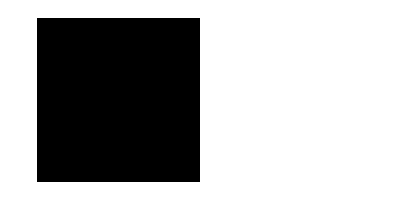
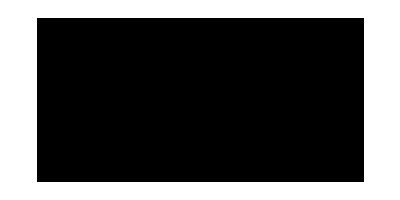
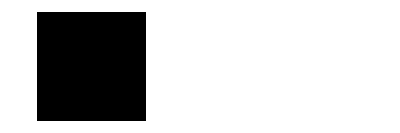
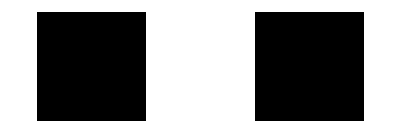
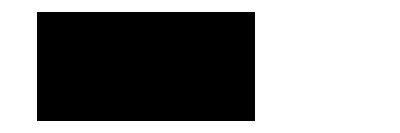
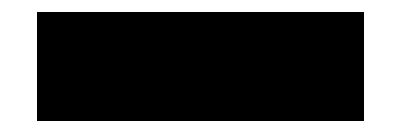
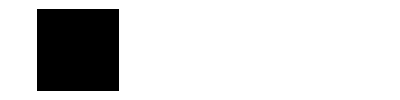
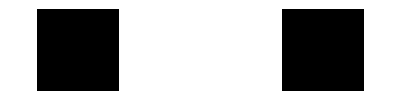
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
ArrayPlot/@List/@IntegerDigits[Range[265],2]//TableForm
```

```mathematica
{CellularAutomaton[124,{{1},0},500]//ArrayPlot,CellularAutomaton[110,{{1},0},500]//ArrayPlot}
```

{-Graphics-,-Graphics-}

```mathematica
IntegerDigits[{110,124},2]
```

```mathematica
ArrayPlot[{#}]&/@{{1,1,0,1,1,1,0},{1,1,1,1,1,0,0}}
```

{-Graphics-,-Graphics-}

```mathematica
{0,0,1,0,0,0,1}//FromDigits[#,2]&
```

17

```mathematica
{0,1,1,1,0,1,1}//FromDigits[#,2]&
```

59

```mathematica
a=1;{a++,BaseForm[a,2],ArrayPlot[#]}&/@Table[CellularAutomaton[n,{{1},0},50],{n,255}]
```

{{1,10_2,-Graphics-},{2,11_2,-Graphics-},{3,100_2,-Graphics-},{4,101_2,-Graphics-},{5,110_2,-Graphics-},{6,111_2,-Graphics-},{7,1000_2,-Graphics-},{8,1001_2,-Graphics-},{9,1010_2,-Graphics-},{10,1011_2,-Graphics-},{11,1100_2,-Graphics-},{12,1101_2,-Graphics-},{13,1110_2,-Graphics-},{14,1111_2,-Graphics-},{15,10000_2,-Graphics-},{16,10001_2,-Graphics-},{17,10010_2,-Graphics-},{18,10011_2,-Graphics-},{19,10100_2,-Graphics-},{20,10101_2,-Graphics-},{21,10110_2,-Graphics-},{22,10111_2,-Graphics-},{23,11000_2,-Graphics-},{24,11001_2,-Graphics-},{25,11010_2,-Graphics-},{26,11011_2,-Graphics-},{27,11100_2,-Graphics-},{28,11101_2,-Graphics-},{29,11110_2,-Graphics-},{30,11111_2,-Graphics-},{31,100000_2,-Graphics-},{32,100001_2,-Graphics-},{33,100010_2,-Graphics-},{34,100011_2,-Graphics-},{35,100100_2,-Graphics-},{36,100101_2,-Graphics-},{37,100110_2,-Graphics-},{38,100111_2,-Graphics-},{39,101000_2,-Graphics-},{40,101001_2,-Graphics-},{41,101010_2,-Graphics-},{42,101011_2,-Graphics-},{43,101100_2,-Graphics-},{44,101101_2,-Graphics-},{45,101110_2,-Graphics-},{46,101111_2,-Graphics-},{47,110000_2,-Graphics-},{48,110001_2,-Graphics-},{49,110010_2,-Graphics-},{50,110011_2,-Graphics-},{51,110100_2,-Graphics-},{52,110101_2,-Graphics-},{53,110110_2,-Graphics-},{54,110111_2,-Graphics-},{55,111000_2,-Graphics-},{56,111001_2,-Graphics-},{57,111010_2,-Graphics-},{58,111011_2,-Graphics-},{59,111100_2,-Graphics-},{60,111101_2,-Graphics-},{61,111110_2,-Graphics-},{62,111111_2,-Graphics-},{63,1000000_2,-Graphics-},{64,1000001_2,-Graphics-},{65,1000010_2,-Graphics-},{66,1000011_2,-Graphics-},{67,1000100_2,-Graphics-},{68,1000101_2,-Graphics-},{69,1000110_2,-Graphics-},{70,1000111_2,-Graphics-},{71,1001000_2,-Graphics-},{72,1001001_2,-Graphics-},{73,1001010_2,-Graphics-},{74,1001011_2,-Graphics-},{75,1001100_2,-Graphics-},{76,1001101_2,-Graphics-},{77,1001110_2,-Graphics-},{78,1001111_2,-Graphics-},{79,1010000_2,-Graphics-},{80,1010001_2,-Graphics-},{81,1010010_2,-Graphics-},{82,1010011_2,-Graphics-},{83,1010100_2,-Graphics-},{84,1010101_2,-Graphics-},{85,1010110_2,-Graphics-},{86,1010111_2,-Graphics-},{87,1011000_2,-Graphics-},{88,1011001_2,-Graphics-},{89,1011010_2,-Graphics-},{90,1011011_2,-Graphics-},{91,1011100_2,-Graphics-},{92,1011101_2,-Graphics-},{93,1011110_2,-Graphics-},{94,1011111_2,-Graphics-},{95,1100000_2,-Graphics-},{96,1100001_2,-Graphics-},{97,1100010_2,-Graphics-},{98,1100011_2,-Graphics-},{99,1100100_2,-Graphics-},{100,1100101_2,-Graphics-},{101,1100110_2,-Graphics-},{102,1100111_2,-Graphics-},{103,1101000_2,-Graphics-},{104,1101001_2,-Graphics-},{105,1101010_2,-Graphics-},{106,1101011_2,-Graphics-},{107,1101100_2,-Graphics-},{108,1101101_2,-Graphics-},{109,1101110_2,-Graphics-},{110,1101111_2,-Graphics-},{111,1110000_2,-Graphics-},{112,1110001_2,-Graphics-},{113,1110010_2,-Graphics-},{114,1110011_2,-Graphics-},{115,1110100_2,-Graphics-},{116,1110101_2,-Graphics-},{117,1110110_2,-Graphics-},{118,1110111_2,-Graphics-},{119,1111000_2,-Graphics-},{120,1111001_2,-Graphics-},{121,1111010_2,-Graphics-},{122,1111011_2,-Graphics-},{123,1111100_2,-Graphics-},{124,1111101_2,-Graphics-},{125,1111110_2,-Graphics-},{126,1111111_2,-Graphics-},{127,10000000_2,-Graphics-},{128,10000001_2,-Graphics-},{129,10000010_2,-Graphics-},{130,10000011_2,-Graphics-},{131,10000100_2,-Graphics-},{132,10000101_2,-Graphics-},{133,10000110_2,-Graphics-},{134,10000111_2,-Graphics-},{135,10001000_2,-Graphics-},{136,10001001_2,-Graphics-},{137,10001010_2,-Graphics-},{138,10001011_2,-Graphics-},{139,10001100_2,-Graphics-},{140,10001101_2,-Graphics-},{141,10001110_2,-Graphics-},{142,10001111_2,-Graphics-},{143,10010000_2,-Graphics-},{144,10010001_2,-Graphics-},{145,10010010_2,-Graphics-},{146,10010011_2,-Graphics-},{147,10010100_2,-Graphics-},{148,10010101_2,-Graphics-},{149,10010110_2,-Graphics-},{150,10010111_2,-Graphics-},{151,10011000_2,-Graphics-},{152,10011001_2,-Graphics-},{153,10011010_2,-Graphics-},{154,10011011_2,-Graphics-},{155,10011100_2,-Graphics-},{156,10011101_2,-Graphics-},{157,10011110_2,-Graphics-},{158,10011111_2,-Graphics-},{159,10100000_2,-Graphics-},{160,10100001_2,-Graphics-},{161,10100010_2,-Graphics-},{162,10100011_2,-Graphics-},{163,10100100_2,-Graphics-},{164,10100101_2,-Graphics-},{165,10100110_2,-Graphics-},{166,10100111_2,-Graphics-},{167,10101000_2,-Graphics-},{168,10101001_2,-Graphics-},{169,10101010_2,-Graphics-},{170,10101011_2,-Graphics-},{171,10101100_2,-Graphics-},{172,10101101_2,-Graphics-},{173,10101110_2,-Graphics-},{174,10101111_2,-Graphics-},{175,10110000_2,-Graphics-},{176,10110001_2,-Graphics-},{177,10110010_2,-Graphics-},{178,10110011_2,-Graphics-},{179,10110100_2,-Graphics-},{180,10110101_2,-Graphics-},{181,10110110_2,-Graphics-},{182,10110111_2,-Graphics-},{183,10111000_2,-Graphics-},{184,10111001_2,-Graphics-},{185,10111010_2,-Graphics-},{186,10111011_2,-Graphics-},{187,10111100_2,-Graphics-},{188,10111101_2,-Graphics-},{189,10111110_2,-Graphics-},{190,10111111_2,-Graphics-},{191,11000000_2,-Graphics-},{192,11000001_2,-Graphics-},{193,11000010_2,-Graphics-},{194,11000011_2,-Graphics-},{195,11000100_2,-Graphics-},{196,11000101_2,-Graphics-},{197,11000110_2,-Graphics-},{198,11000111_2,-Graphics-},{199,11001000_2,-Graphics-},{200,11001001_2,-Graphics-},{201,11001010_2,-Graphics-},{202,11001011_2,-Graphics-},{203,11001100_2,-Graphics-},{204,11001101_2,-Graphics-},{205,11001110_2,-Graphics-},{206,11001111_2,-Graphics-},{207,11010000_2,-Graphics-},{208,11010001_2,-Graphics-},{209,11010010_2,-Graphics-},{210,11010011_2,-Graphics-},{211,11010100_2,-Graphics-},{212,11010101_2,-Graphics-},{213,11010110_2,-Graphics-},{214,11010111_2,-Graphics-},{215,11011000_2,-Graphics-},{216,11011001_2,-Graphics-},{217,11011010_2,-Graphics-},{218,11011011_2,-Graphics-},{219,11011100_2,-Graphics-},{220,11011101_2,-Graphics-},{221,11011110_2,-Graphics-},{222,11011111_2,-Graphics-},{223,11100000_2,-Graphics-},{224,11100001_2,-Graphics-},{225,11100010_2,-Graphics-},{226,11100011_2,-Graphics-},{227,11100100_2,-Graphics-},{228,11100101_2,-Graphics-},{229,11100110_2,-Graphics-},{230,11100111_2,-Graphics-},{231,11101000_2,-Graphics-},{232,11101001_2,-Graphics-},{233,11101010_2,-Graphics-},{234,11101011_2,-Graphics-},{235,11101100_2,-Graphics-},{236,11101101_2,-Graphics-},{237,11101110_2,-Graphics-},{238,11101111_2,-Graphics-},{239,11110000_2,-Graphics-},{240,11110001_2,-Graphics-},{241,11110010_2,-Graphics-},{242,11110011_2,-Graphics-},{243,11110100_2,-Graphics-},{244,11110101_2,-Graphics-},{245,11110110_2,-Graphics-},{246,11110111_2,-Graphics-},{247,11111000_2,-Graphics-},{248,11111001_2,-Graphics-},{249,11111010_2,-Graphics-},{250,11111011_2,-Graphics-},{251,11111100_2,-Graphics-},{252,11111101_2,-Graphics-},{253,11111110_2,-Graphics-},{254,11111111_2,-Graphics-},{255,100000000_2,-Graphics-}}

```mathematica
ArrayPlot[CellularAutomaton[#,{{1},0},1000]]&/@{110,124,137,193}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{110,124,137,193}//FactorInteger
```

{{{2,1},{5,1},{11,1}},{{2,2},{31,1}},{{137,1}},{{193,1}}}

{1101110_2,1111100_2,10001001_2,11000001_2}

```mathematica
{Range[28]}//MatrixPlot
```

-Graphics-